## From Riccardo:

```mathematica
(* Probs not needed *)
```

```mathematica
argumentLength[func_Symbol] := Lookup[SyntaxInformation[func], "ArgumentsPattern"]
argumentLength["Plot"]
```

## From Giulio and Tim:

### General:

```mathematica
WolframLanguageData["Exp","DocumentationExampleInputs"]
```

```mathematica
SyntaxInformation[Exp]
```

### Defined functions:

```mathematica
(* No longer useful *)
```

```mathematica
parseString[str_String]:=FrontEndExecute[FrontEnd`ReparseBoxStructurePacket[str]];
```

```mathematica
flattenParse[exp_]:=Flatten@ReplaceRepeated[exp, RowBox[{anything___}]:>{anything}]
```

```mathematica
SetAttributes[makeExpressionString, {HoldFirst}]
makeExpressionString[exp_]:=StringTake[ToString[HoldComplete[exp], InputForm], {StringLength["HoldComplete["]+1,-StringLength["]"]-1}]
```

```mathematica
(*functionargs[function_]:=Length/@Map[Select[SyntaxInformation[function][[1,2]],#]&,{#==_&,#==_.&,#==OptionsPattern[]&}];*)
```

```mathematica
functionargs[function_String] := functionargs[Symbol[function]]
functionargs[function_Symbol]:=Length/@Map[Select[Lookup[SyntaxInformation[function], "ArgumentsPattern"],#]&,{#==_&,#==_||#==_.||#==OptionsPattern[]&}];
```

## From Giulio regarding parsing:

```mathematica
ClearAll["Global`*"]
```

#### Convert the expression to a tree structure, regardless of whether it parses or not:

```mathematica
parseInput[str_String]:=ReplaceAll[Replace[FrontEndExecute[FrontEnd`ReparseBoxStructurePacket[str]],RowBox[x_]:>x,{0,Infinity}]," ":> Nothing];
```

```mathematica
(*takepart[expr_String,level_Integer]:=Replace[level[parseInput[expr],{level}],x_/;!AtomQ[x]:>Head[x],{1}]*)
```

#### Get slices of the expression:

```mathematica
getlevel[expr_String,n_Integer]:=With[{el=n},Replace[Level[parseInput[expr],{el}],x_/;!AtomQ[x]:>ToString[Head[x]],{1}]]
```

#### Get all the tree structure of the expression:

```mathematica
getalllevels[expr_String]:=Thread[getlevel[expr,Range[Depth[parseInput[expr]]-1]]];
```

#### functionargs returns the minimum and maximum number of arguments a function can have

#### Playing with uneven number of brackets:

```mathematica
mystring="SortBy[Range[10], Mod[#,3&]";
```

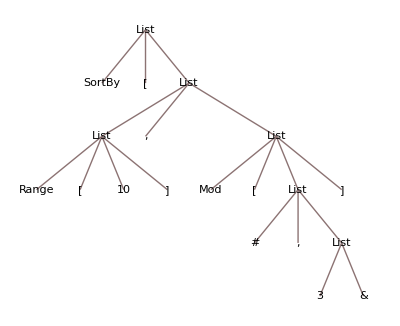

```mathematica
parseInput[mystring]//TreeForm
```

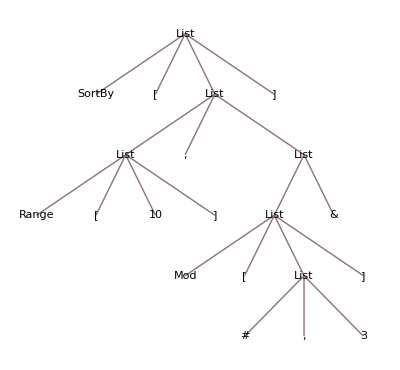

```mathematica
parseInput[mystring]//TreeForm
```

```mathematica
alllevels= getalllevels[mystring];alllevels//Column
```

{SortBy,[,List,]}
{List,,,List}
{Range,[,10,],List,&}
{Mod,[,List,]}
{#,,,3}

```mathematica
listA=Total/@Map[StringCount[#,"["]&,alllevels,{2}]
```

{1,0,1,1,0}

```mathematica
listB=Total/@Map[StringCount[#,"]"]&,alllevels,{2}]
```

{1,0,1,1,0}

```mathematica
Positive[listA-listB]
```

{False,False,False,False,False}

```mathematica
Negative[listA-listB]
```

{False,False,False,False,False}

```mathematica
MapThread[Greater,{listA,listB}]
```

{False,False,False,False,False}

#### Count the # arguments in functions:

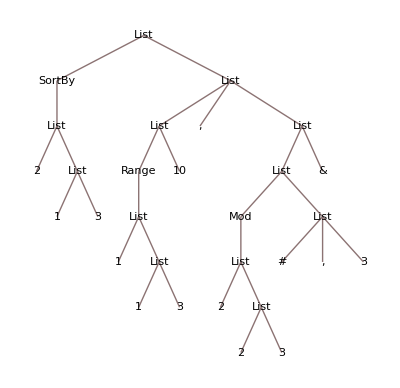

```mathematica
myexpr//. {upper___,function_,open_,body___,close_,lower___}/; open=="["&&close=="]"  :> { function[{1+Length@Cases[","]@body,functionargs[function]}], body, lower}//TreeForm
```

#### Other stuff:

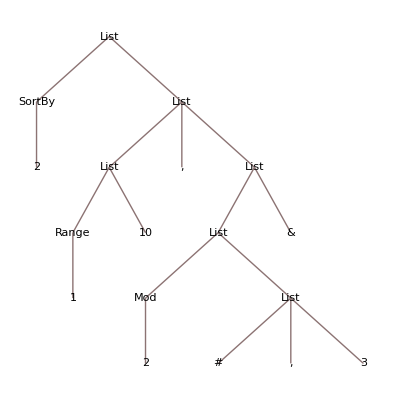

```mathematica
myexpr//. {upper___,function_,open_,body___,close_,lower___}/; open=="["&&close=="]"  :> {upper, function[1+Length@Cases[","]@body], body, lower}//TreeForm
```

```mathematica
(*/;Echo[{body,Length[body]},"Body Length"] *)
```

```mathematica
Cases[myexpr,{___,open_,body___,close_,___},Depth[myexpr]]//Column
```

{Range,[,10,]}
{#,,,3}
{Mod,[,{#,,,3},]}
{{Mod,[,{#,,,3},]},&}
{{Range,[,10,]},,,{{Mod,[,{#,,,3},]},&}}

10

## Back to Tim’s Idea:

### (* Convert an expression to a flattened String and try to build the tree correctly *)

#### Initialise:

```mathematica
mystring=makeExpressionString["SortBy[Range[π Cos[10.3]], Mod[#1, 3 & ]]"]
```

"SortBy[Range[π Cos[10.3]], Mod[#1, 3 & ]]"

```mathematica
SortBy[Range[π Cos[10.3]], Mod[#1, 3 & ]]//Hold//TreeForm
```

#### Loop Over:

```mathematica
(* Trouble when a functions name is composed out of two other function names: eg IntegerPart -> Integet and Part are also funtions *)
```

```mathematica
(* Take the indexes of the functions that have a head which is a known function and are between brackets. Also they shouldn't include any subfunctions *)
```

```mathematica
(* Not[StringContainsQ[body,"Argument"]]&& *)
```

```mathematica
ranges=StringPosition[mystring,head__~~"["~~body___~~"]"
/; {head}==Names[head]
(*&&StringCases[body,xx__/;Names[xx]=={xx}]=={}*)
(*&& Names[body]== {}*)&&StringCount[body,"["]==StringCount[body,"]"],
Overlaps->All]; ranges//Column
```

{2,41}
{9,40}
{9,25}
{28,40}

#### From Giulio:

```mathematica
a[a[a[a[]]]]
```

a[a[a[a[]]]]

```mathematica
str="a[b[], foo[g[Plot[]]]]";
```

```mathematica
level=0;
head=None;
Reap[StringCases[str,{
"[":>Sow[Print["current head is: ", head];level++,"level"],
"]":>Sow[Print["current head is: ", head];level--,"level"],
h:LetterCharacter..:>Sow[head=h,"head"]}
];,_,Rule]
```

current head is: a

current head is: b

current head is: b

current head is: foo

current head is: g

current head is: Plot

current head is: Plot

current head is: Plot

«2 more identical outputs»

{Null,{head→{a,b,foo,g,Plot},level→{0,1,2,1,2,3,4,3,2,1}}}

```mathematica
Join[
Thread[StringPosition[str,"["][[All,1]]->1],
Thread[StringPosition[str,"]"][[All,1]]->-1]
]//KeySort
```

<|2→1,4→1,5→-1,9→1,11→1,13→1,14→-1,15→-1,16→-1,17→-1|>

```mathematica
Accumulate[Values@%]
```

{1,2,1,2,3,4,3,2,1,0}

```mathematica
Plus[Cos[1,2],3]
```

```mathematica
Plus[Cos[1],2,3]
```

```mathematica
Thread[StringPosition[str,"]"][[All,1]]->-1]
```

{5→-1,14→-1,15→-1,16→-1,17→-1}

```mathematica
functions=StringTake[mystring,ranges];functions//Column
```

SortBy[Range[π argument], Mod[#1, 3 & ]]
Range[π argument], Mod[#1, 3 & ]
Range[π argument]
Mod[#1, 3 & ]

```mathematica
(* Count the arguments each function has *)
```

```mathematica
argnumbers=StringCount[functions,","]+1;argnumbers
```

{1,2}

```mathematica
(* Count the arguments each function should have *)
```

```mathematica
idealargnumbers=functionargs/@Flatten@StringCases[functions,head__ /; {head}==Names[head]:> head]
```

{{1,3},{2,3}}

```mathematica
(* Check if any of the functions has exactly the number of arguments that should be used as input *)
```

```mathematica
exactarguments=Table[{{argnumbers[[i]]}==(Range@@@idealargnumbers)[[i]]},{i,Length[argnumbers]}]//Flatten
```

{False,False}

```mathematica
(* When the arguments are exactly correct, replace with the the string "argument" so it doesn't get picked up again *)
```

```mathematica
(* TO DO: Find the Wolfram whay to do it *)
```

```mathematica
tempstring=mystring;
```

```mathematica
Do[tempstring=StringReplace[tempstring,functions[[ii]]/; exactarguments[[ii]]->"argument"],{ii,Length[argnumbers]}]
```

```mathematica
mystring=tempstring
```

"SortBy[Range[π argument], Mod[#1, 3 & ]]"

## Giulio 3/07

```mathematica
(*
```

```mathematica
level
```

```mathematica
inPartlevel
```

```mathematica
inString
```

```mathematica
inComment
```

```mathematica
{head,argcount,id}
```

```mathematica
j[[
```

```mathematica
[
```

```mathematica
]]
```

```mathematica
,
```

```mathematica
{"w",22->"]"}
```

```mathematica
{"w",-1->"]"}
```

```mathematica
f[[]
```

```mathematica
mystring
```

"SortBy[Range[π Argument], Mod[#1, 3 & ]]"

```mathematica
ranges=StringPosition[mystring,head__~~"["~~body___~~"]"/;Not[StringContainsQ[body,"Argument"]]&& {head}==Names[head]&&StringCases[body,xx__/;Names[xx]=={xx}]=={}&& Names[body]== {}&&StringCount[body,"["]==StringCount[body,"]"],Overlaps->All]; ranges//Column
```

{17,25}
{29,41}

```mathematica
functions=StringTake[mystring,ranges];functions//Column
```

Cos[10.3]
Mod[#1, 3 & ]

```mathematica
Names["Range[IntegerPart[10.3]], Mod[#1, 3 & ]"]
```

{}

```mathematica
StringCases["Range[IntegerPart[10.3]], Mod[#1, 3 & ]",xx__/; Names[xx]=={xx}]
```

{Range,IntegerPart,Mod}

```mathematica
||Echo[{StringCases[body,xx__/;Names[xx]=={xx}],StringCount[body,"["],StringCount[body,"]"]}]
```

```mathematica
(* Delete the rest *)
```

```mathematica
ranges//Column
```

{17,25}
{29,41}

```mathematica
functions=StringTake[mystring,ranges];functions//Column
```

SortBy[Range[π Cos[10.3]], Mod[#1, 3 & ]]
SortBy[Range[π Cos[10.3]], Mod[#1, 3 & ]
SortBy[Range[π Cos[10.3]]
SortBy[Range[π Cos[10.3]
Range[π Cos[10.3]], Mod[#1, 3 & ]]
Range[π Cos[10.3]], Mod[#1, 3 & ]
Range[π Cos[10.3]]
Range[π Cos[10.3]
Cos[10.3]], Mod[#1, 3 & ]]
Cos[10.3]], Mod[#1, 3 & ]
Cos[10.3]]
Cos[10.3]
Mod[#1, 3 & ]]
Mod[#1, 3 & ]

```mathematica
StringCases["Range[π Cos[10.3]], Mod[#1, 3 & ]]","["~~"]"]
```

{}

```mathematica
<|2->{2,3},1->{ 3,4}|>
```

<|2→{2,3},1→{3,4}|>

```mathematica
%35[2]
```

{2,3}

## Before meeting with Tim:

Implement: {head, argcount, id}

```mathematica
str="a[b[],foo[g[Plot[]]]]";
```

```mathematica
str="a[b[cc[d[e[foo[t, h[x]]]]]]]";
```

```mathematica
str=mystring
```

"SortBy[Range[π Cos[10.3]], Mod[#1, 3 & ]]"

```mathematica
level=0;head=None;previousheads=<| |>;id=0;
Reap[StringCases[str,{
"[":>
Sow[Print[previousheads],
level++;
id++;
previousheads=Append[id-> {head,1}]@previousheads;
Print["current level, head is: ",level," ", head];],
"]":>Sow[Print[previousheads],level--;
If[level>0,head=previousheads[id][[1]]];Print["current level, head is: ",level," ", head];],
h:LetterCharacter..:>Sow[head=h,"head"],
",":> Sow[Print["A comma was found"];Append[previousheads,id-> previousheads[id][[2]]+1]
(*previousheads[id][[2]]++*)]}
];,_,Rule]
```

<||>

current level, head is: 1 SortBy

<|1→{SortBy,1}|>

current level, head is: 2 Range

<|1→{SortBy,1},2→{Range,1}|>

current level, head is: 3 Cos

<|1→{SortBy,1},2→{Range,1},3→{Cos,1}|>

current level, head is: 2 Cos

<|1→{SortBy,1},2→{Range,1},3→{Cos,1}|>

current level, head is: 1 Cos

A comma was found

<|1→{SortBy,1},2→{Range,1},3→{Cos,1}|>

current level, head is: 2 Mod

A comma was found

<|1→{SortBy,1},2→{Range,1},3→{Cos,1},4→{Mod,1}|>

current level, head is: 1 Mod

<|1→{SortBy,1},2→{Range,1},3→{Cos,1},4→{Mod,1}|>

current level, head is: 0 Mod

{Null,{head→{SortBy,Range,π,Cos,Mod},Null→{Null,Null,Null,Null,Null,Null,Null,Null},None→{<|1→{SortBy,1},2→{Range,1},3→2|>,<|1→{SortBy,1},2→{Range,1},3→{Cos,1},4→2|>}}}

# Fix the reason why all show one argument

```mathematica
previousheads//Values//Column
```

{SortBy,1}
{Range,1}
{Cos,1}
{Mod,1}

current level, head is: 1 SortBy

<|1→{SortBy,1}|>

current level, head is: 2 Range

<|1→{SortBy,1},2→{Range,1}|>

current level, head is: 3 Cos

<|1→{SortBy,1},2→{Range,1},3→{Cos,1}|>

current level, head is: 2 Cos

<|1→{SortBy,1},2→{Range,1},3→{Cos,1}|>

current level, head is: 1 Cos

A comma was found

<|1→{SortBy,1},2→{Range,1},3→{Cos,1}|>

current level, head is: 2 Mod

A comma was found

<|1→{SortBy,1},2→{Range,1},3→{Cos,1},4→{Mod,1}|>

current level, head is: 1 Mod

<|1→{SortBy,1},2→{Range,1},3→{Cos,1},4→{Mod,1}|>

current level, head is: 0 Mod

{Null,{head→{SortBy,Range,π,Cos,Mod},Null→{Null,Null,Null,Null,Null,Null,Null,Null},None→{Null,Null}}}

```mathematica
previousheads[4][[1]]
```

Mod

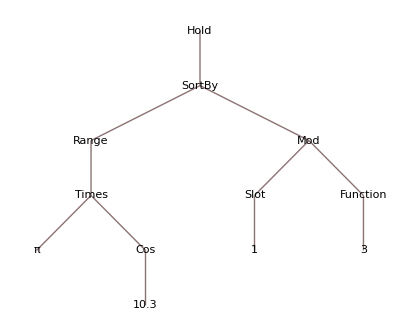

```mathematica
SortBy[Range[π Cos[10.3]], Mod[#1, 3 & ]]//Hold//TreeForm
```

```mathematica
previousheads//Column
```

{SortBy,2}
{Range,2}
{Cos,1}
{Mod,1}

```mathematica
Reap[StringCases[str,{
"[", "]", h:LetterCharacter..:>Sow[head=h,"head"]}
];,_,Rule]
```

{Null,{head→{a,b,cc,d,e,foo,t,h,x}}}

```mathematica
previousheads
```

{a,b,cc,d,e,foo,h}

```mathematica
SyntaxInformation[AASTriangle]
```

```mathematica
{"ArgumentsPattern"->{_,_,_}}
```

```mathematica
symbolsWithInfo = GroupBy[Names["System`*"][[117;;]], Lookup[Association[SyntaxInformation[Symbol[#]]],"ArgumentsPattern"]=!={___}&]
```

```mathematica
Length@Names["System`*"][[117;;]]
```

6490

```mathematica
Length@symbolsWithInfo
```

6350

```mathematica
f[g[h[a,b,c],t]
```

```mathematica
symbolsSignatures = GroupBy[Names["System`*"][[117;;]], Lookup[Association[SyntaxInformation[Symbol[#]]],"ArgumentsPattern"]&]
```

<|{_,_,_}→{AASTriangle,AdjustTimeSeriesForecast,ASATriangle,AsynchronousTaskObject,BeniniDistribution,BernsteinBasis,BetaBinomialDistribution,BetaNegativeBinomialDistribution,DagumDistribution,DirichletCharacter,DirichletL,ExpGammaDistribution,GeometricBrownianMotionProcess,HjorthDistribution,HurwitzLerchPhi,Hypergeometric1F1,Hypergeometric1F1Regularized,HypergeometricDistribution,HypergeometricU,InverseLaplaceTransform,LinearRecurrence,LinkObject,LogGammaDistribution,MathieuC,MathieuCPrime,MathieuS,MathieuSPrime,MaxStableDistribution,MinStableDistribution,Nest,NestList,NetInsert,NoncentralBetaDistribution,PowerMod,PowerModList,PowersRepresentations,QBinomial,SampledSoundFunction,SASTriangle,ShearingMatrix,SinghMaddalaDistribution,SpheroidalEigenvalue,SpheroidalJoiningFactor,SpheroidalRadialFactor,SSSTriangle,StringInsert,Subsuperscript,TagSet,TagSetDelayed,TransformedField,Underoverscript,WhittakerM,WhittakerW,XMLElement,ZernikeR},{{__}}→{AbelianGroup,Catenate,Control,Cycles,EntityGroup,ExternalBundle,FromPolarCoordinates,FromSphericalCoordinates,KeyIntersection,KeyValuePattern,LatticeReduce,MeanAround,RowBox,SocketWaitAll,SocketWaitNext,SystemsModelMerge,ToPolarCoordinates,ToSphericalCoordinates,URLDispatcher,WaitNext},{}→{Abort,AbortKernels,AskState,AsynchronousTasks,BabyMonsterGroupB,Beep,Break,ButtonNotebook,ChannelListeners,CloudDirectory,Continue,ConwayGroupCo1,ConwayGroupCo2,ConwayGroupCo3,CreateTemporary,Databins,Directory,DirectoryStack,DisplayEndPacket,DisplayPacket,DocumentGenerators,End,EndAdd,EndPackage,EntityStores,EvaluationBox,EvaluationCell,EvaluationNotebook,FinishDynamic,FischerGroupFi22,FischerGroupFi23,FischerGroupFi24Prime,HaarWavelet,HaradaNortonGroupHN,HeldGroupHe,HigmanSimsGroupHS,InputNotebook,InputPacket,InputStringPacket,InstanceNormalizationLayer,Interrupt,JankoGroupJ1,JankoGroupJ2,JankoGroupJ3,JankoGroupJ4,Kernels,LyonsGroupLy,MathieuGroupM11,MathieuGroupM12,MathieuGroupM22,MathieuGroupM23,MathieuGroupM24,McLaughlinGroupMcL,MemoryAvailable,MonsterGroupM,MorletWavelet,MouseButtons,ONanGroupON,Overflow,PermissionsGroups,Processes,ResetDirectory,ResumePacket,RudvalisGroupRu,ScheduledTasks,SearchIndices,SelectedNotebook,SessionTime,SuspendPacket,SuzukiGroupSuz,Tasks,ThompsonGroupTh,TimeUsed,TimeZone,TitsGroupT,TraceLevel,Underflow,WebSessions},{_}→{AbortProtect,AbortScheduledTask,Abs,AbsArg,AbsoluteDashing,AbsoluteFileName,AbsolutePointSize,AbsoluteThickness,AbsoluteTiming,Accuracy,AcyclicGraphQ,AdjacencyMatrix,AffineTransform,AiryAi,AiryAiPrime,AiryBi,AiryBiPrime,AlgebraicIntegerQ,AlgebraicNumberDenominator,AlgebraicUnitQ,AlphaChannel,AlternatingFactorial,AlternatingGroup,Antonyms,ArcCos,ArcCosh,ArcCot,ArcCoth,ArcCsc,ArcCsch,ArcSec,ArcSech,ArcSin,ArcSinh,ArcTanh,Arg,Ask,AskAppend,AskDisplay,AskedQ,AskedValue,AskTemplateDisplay,AssociationQ,AtomQ,Attributes,AudioChannels,AudioLength,AudioQ,AudioSampleRate,AudioType,AutoSubmitting,BarlowProschanImportance,BarnesG,BartlettHannWindow,BartlettWindow,BaseDecode,BaseEncode,Begin,BeginDialogPacket,BenfordDistribution,BernoulliDistribution,BernoulliProcess,BetweennessCentrality,BinaryImageQ,BinomialProcess,BipartiteGraphQ,BitLength,BitNot,BlackmanHarrisWindow,BlackmanNuttallWindow,BlackmanWindow,BlockchainGet,BlockchainPut,BlockchainTransaction,BlockchainTransactionSubmit,BohmanWindow,Boole,BooleanQ,BooleanVariables,BoundaryMeshRegionQ,BoundedRegionQ,BoxData,BoxObject,ByteArray,ByteArrayFormat,ByteArrayQ,ByteCount,CanonicalGraph,CanonicalizePolyhedron,CanonicalName,CantorStaircase,CapForm,CapitalDifferentialD,CarmichaelLambda,CaseSensitive,CatalanNumber,CellObject,CellPrint,CForm,Characters,ChiDistribution,ChiSquareDistribution,CholeskyDecomposition,CircularOrthogonalMatrixDistribution,CircularQuaternionMatrixDistribution,CircularRealMatrixDistribution,CircularSymplecticMatrixDistribution,CircularUnitaryMatrixDistribution,Circumsphere,ClearCookies,Close,ClosenessCentrality,ColorNegate,ColorQ,CommonName,CompoundElement,Conjugate,ConnectedGraphQ,ConnectedMoleculeComponents,ConnectedMoleculeQ,ConstantRegionQ,ContextToFileName,ContinuousTimeModelQ,ControllabilityMatrix,ConvexPolygonQ,ConvexPolyhedronQ,CopyToClipboard,Cos,Cosh,CoshIntegral,CosIntegral,Cot,Coth,CountDistinct,Counts,Csc,Csch,CubeRoot,CyclicGroup,Dashing,DatabaseConnect,DatabaseReference,Dataset,DateBounds,DateObjectQ,DawsonF,Decapitalize,Decrement,DedekindEta,Defer,Definition,Del,DeleteCloudExpression,DeleteFile,DeleteObject,DeleteSearchIndex,DeleteStopwords,Deploy,DerivedKey,DeviceClose,DifferenceRoot,DifferentialD,DigitQ,DihedralGroup,DirectedGraphQ,DirectoryQ,DirichletBeta,DirichletEta,DirichletLambda,DirichletWindow,DisableFormatting,DiscreteTimeModelQ,DisplayForm,DistributionParameterAssumptions,DistributionParameterQ,DMSList,DotPlusLayer,DualSystemsModel,DumpGet,Duration,EccentricityCentrality,EdgeBetweennessCentrality,EdgeCycleMatrix,EdgeRules,EdgeWeightedGraphQ,EllipticK,EllipticNomeQ,EmbeddedService,EmitSound,EmpiricalDistribution,EmptyGraphQ,EmptyRegion,EndDialogPacket,EnterExpressionPacket,EnterTextPacket,EntityClassList,EntityProperties,EntityRegister,EntityTypeName,EntityUnregister,Environment,EqualTo,Erfc,Erfi,ErrorBox,EulerCharacteristic,EulerianGraphQ,EulerPhi,EvaluatePacket,EvaluateScheduledTask,EvaluationData,EvenQ,ExactBlackmanWindow,ExactNumberQ,Exp,ExpandFileName,ExpIntegralEi,ExponentialDistribution,ExpToTrig,Factorial,Factorial2,FailureQ,Fibonorial,File,FileByteCount,FileExistsQ,FileSize,FileType,FindEdgeCover,FindFile,FindLibrary,FindVertexCover,FiniteAbelianGroupCount,FiniteGroupCount,FlatTopWindow,FortranForm,FractionalPart,FresnelC,FresnelF,FresnelG,FresnelS,FromContinuedFraction,FromDate,FromDMS,FromEntity,FromRomanNumeral,FrontEndExecute,FullAxes,FullDefinition,FullGraphics,FullRegion,GeoAntipode,GeoGroup,GeometricDistribution,GeometricMean,GeoVector,GeoVectorENU,GeoVectorXYZ,GeoVisibleRegion,GeoVisibleRegionBoundary,GetContext,GlobalClusteringCoefficient,Goto,GrammarToken,GraphAutomorphismGroup,GraphCenter,GraphLinkEfficiency,GraphQ,GraphRadius,GreaterEqualThan,GreaterThan,GroupGenerators,GroupMultiplicationTable,GroupOrder,Gudermannian,HalfNormalDistribution,HamiltonianGraphQ,HammingWindow,HarmonicMean,Haversine,Head,HoldForm,HoldPattern,HTTPErrorResponse,Hyperfactorial,Identity,IgnoringInactive,Im,ImageAspectRatio,ImageChannels,ImageColorSpace,ImageDimensions,ImageQ,ImageType,Inactive,IncidenceMatrix,Increment,IndependentPhysicalQuantity,IndependentUnit,IndependentUnitDimension,InexactNumberQ,InnerPolygon,InnerPolyhedron,InputNamePacket,Insphere,IntegerPart,IntegerQ,InverseEllipticNomeQ,InverseErfc,InverseGudermannian,InverseHaversine,InversePermutation,Invisible,IPAddress,JoinForm,JordanDecomposition,JordanModelDecomposition,KaiserBesselWindow,KernelFunction,Key,KillProcess,KirchhoffMatrix,KleinInvariantJ,KnownUnitQ,Kurtosis,Label,LanczosWindow,LanguageIdentify,LeafCount,Length,LessEqualThan,LessThan,LetterQ,LibraryFunction,LibraryFunctionInformation,LibraryFunctionUnload,LibraryLoad,LibraryUnload,LindleyDistribution,LinearFractionalTransform,LinkActivate,LinkClose,LinkError,LinkFlush,LinkInterrupt,LinkPatterns,LinkReadHeld,ListQ,LocalSymbol,Log10,Log2,LogBarnesG,LogGamma,LogIntegral,LogisticSigmoid,LogSeriesDistribution,LoopFreeGraphQ,LowerCaseQ,MachineNumberQ,MangoldtLambda,MathMLForm,MaxwellDistribution,Mean,MeanClusteringCoefficient,MeanDeviation,Median,MedianDeviation,MersennePrimeExponent,MersennePrimeExponentQ,MeshCoordinates,MeshRegionQ,MessageList,Midpoint,MinimumTimeIncrement,MinkowskiQuestionMark,Minus,MissingQ,MixedFractionParts,MixedGraphQ,ModularLambda,MoebiusMu,MoleculeProperty,MoleculeQ,Most,MultigraphQ,NameQ,NearestFunction,Negative,NegativeDefiniteMatrixQ,NetDecoder,NetEncoder,NetPortGradient,NetSharedArray,NextScheduledTaskTime,NonNegative,NonPositive,Not,NotebookLocate,NotebookTemplate,NumberFieldClassNumber,NumberQ,NumericalSort,NumericArrayQ,NumericArrayType,NumericQ,NuttallWindow,ObservabilityMatrix,OddQ,OptionQ,OuterPolygon,OuterPolyhedron,OutputControllabilityMatrix,OutputForm,OutputNamePacket,OverBar,OverDot,OverHat,OverTilde,OverVector,ParallelNeeds,ParentBox,ParentCell,ParentNotebook,PartitionsP,PartitionsQ,PartOfSpeech,ParzenWindow,PathGraphQ,PauliMatrix,Pause,PerfectNumberQ,PermissionsKey,PermutationCyclesQ,PermutationLength,PermutationListQ,PermutationMax,PermutationMin,PermutationOrder,PermutationSupport,PlanarGraphQ,PointSize,PoissonDistribution,PoissonProcess,PolygonCoordinates,PolyhedronCoordinates,PolyhedronGenus,Polynomials,PositionIndex,Positive,PositiveDefiniteMatrixQ,Precision,PreDecrement,PreemptProtect,PreIncrement,Prime,PrimePi,PrimeZetaP,PrimitiveRootList,PrintableASCIIQ,PrivateKey,ProcessParameterAssumptions,ProcessParameterQ,PublicKey,QuadraticIrrationalQ,QuantityQ,QuantityUnit,QuantityVariableCanonicalUnit,QuantityVariableDimensions,QuantityVariableIdentifier,QuantityVariablePhysicalQuantity,RamanujanTau,RamanujanTauL,RamanujanTauTheta,RamanujanTauZ,Ramp,RawBoxes,RawData,RayleighDistribution,Re,RealAbs,RealSign,ReflectionMatrix,RegionBoundary,RegionEmbeddingDimension,RegionQ,RegularExpression,RegularlySampledQ,ReIm,Reinstall,ReleaseHold,RemoveAsynchronousTask,Removed,RemoveInputStreamMethod,RemoveOutputStreamMethod,RemoveScheduledTask,RenewalProcess,ResourceRemove,Rest,ReturnExpressionPacket,ReturnPacket,ReturnTextPacket,RiemannR,RiemannSiegelTheta,RiemannSiegelZ,RiemannXi,RomanNumeral,RootMeanSquare,RootOfUnityQ,RudinShapiro,Run,ScheduledTaskActiveQ,ScorerGi,ScorerGiPrime,ScorerHi,ScorerHiPrime,SearchIndexObject,SearchQueryString,Sec,Sech,SecuredAuthenticationKey,ServiceDisconnect,SetCookies,SetEnvironment,SetSelectedNotebook,SetSystemOptions,Setting,ShortestMatch,ShortTimeFourierData,Sign,Signature,SimpleGraphQ,SimplePolygonQ,SimplePolyhedronQ,Sin,Sinc,Sinh,SinhIntegral,SinIntegral,Skeleton,Skewness,SmithDecomposition,SolidRegionQ,SpaceForm,Spacer,SpherePoints,Sqrt,Square,SquareMatrixQ,StackBegin,StackComplete,StackInhibit,StandardDeviation,StandardForm,StartAsynchronousTask,StartExternalSession,StartProcess,StartScheduledTask,StationaryDistribution,StopAsynchronousTask,StopScheduledTask,StreamPosition,StringByteCount,StringFormat,StringLength,StringQ,StringReverse,StringSkeleton,StringToStream,StripBoxes,Subfactorial,SubMinus,SubPlus,SubStar,SuperDagger,SuperMinus,SuperPlus,SuperStar,Symbol,SymbolName,SymmetricGroup,SymmetricKey,Synonyms,SyntaxInformation,SyntaxLength,SyntaxPacket,SystemsModelDelay,SystemsModelDimensions,SystemsModelLinearity,SystemsModelOrder,Tan,Tanh,TaskAbort,TaskExecute,TaskObject,TaskRemove,TaskResume,TaskSuspend,TelegraphProcess,TeXForm,TextData,TextPacket,Texture,Thickness,ThueMorse,TimeObjectQ,TimeSeriesInvertibility,Timing,ToDate,ToInvertibleTimeSeries,ToLowerCase,TopologicalSort,ToRules,ToUpperCase,TracyWidomDistribution,TransferFunctionExpand,TransferFunctionFactor,TransformationFunction,TransformationMatrix,TranslationTransform,TreeGraphQ,TrigExpand,TrigFactor,TrigFactorList,TrigToExp,TrueQ,TypeSpecifier,UnderBar,UndirectedGraphQ,UnequalTo,Unevaluated,Uninstall,UnitDimensions,Unset,UpdateSearchIndex,UpperCaseQ,UpTo,URL,UsingFrontEnd,V2Get,ValueQ,Variance,Verbatim,VertexWeightedGraphQ,WaitAll,WeaklyConnectedGraphQ,WeakStationarity,WeightedGraphQ,WordCount,WordDefinition,WordStem,XMLObject,$DisplayFunction,$SoundDisplayFunction},Missing[KeyAbsent,ArgumentsPattern]→{Above,Absolute,AcceptanceThreshold,AccuracyGoal,ActionDelay,ActionMenuBox,ActionMenuBoxOptions,Active,ActiveItem,ActiveStyle,AddOnHelpPath,AdjustmentBoxOptions,After,AlgebraicRules,AlgebraicRulesData,Algebraics,Alignment,AlignmentMarker,AlignmentPoint,All,AllowAdultContent,AllowedCloudExtraParameters,AllowedCloudParameterExtensions,AllowedDimensions,AllowedFrequencyRange,AllowedHeads,AllowGroupClose,AllowIncomplete,AllowInlineCells,AllowKernelInitialization,AllowLooseGrammar,AllowReverseGroupClose,AllowScriptLevelChange,AlternateImage,AlternativeHypothesis,AltitudeMethod,AmbientLight,AmbiguityFunction,Analytic,AnatomySkinStyle,AnchoredSearch,AnimationCycleOffset,AnimationCycleRepetitions,AnimationDirection,AnimationDisplayTime,AnimationRate,AnimationRepetitions,AnimationRunning,AnimationRunTime,AnimationTimeIndex,AnimatorBox,AnimatorBoxOptions,AnimatorElements,Annotate,AnnotationNames,AnnotationRules,AnnotationValue,Anonymous,Antialiasing,Appearance,AppearanceElements,AppearanceRules,AppendCheck,ApplicationIdentificationKey,arraycopy,Arrow3DBox,ArrowBox,AspectRatio,AspectRatioFixed,AssociationFormat,AssociationMap,AssumeDeterministic,Assumptions,Asynchronous,AtomCoordinates,AtomDiagramCoordinates,AudioChannelAssignment,AudioDevice,AudioInputDevice,AudioLabel,AudioLooping,AudioOutputDevice,Authenticate,Authentication,AutoAction,AutoCopy,AutoDelete,AutoEvaluateEvents,AutoGeneratedPackage,AutoIndent,AutoIndentSpacings,AutoItalicWords,AutoloadPath,AutoMatch,Automatic,AutomaticImageSize,AutoMultiplicationSymbol,AutoNumberFormatting,AutoOpenNotebooks,AutoOpenPalettes,AutoQuoteCharacters,AutoRemove,AutorunSequencing,AutoScaling,AutoScroll,AutoSpacing,AutoStyleOptions,AutoStyleWords,Axes,AxesEdge,AxesLabel,AxesOrigin,AxesStyle,AxiomaticTheory,Axis,Back,Background,BackgroundAppearance,BackgroundTasksSettings,Backsubstitution,Backward,BarOrigin,BarSpacing,Baseline,BaselinePosition,BaseStyle,BatchSize,Before,BeginFrontEndInteractionPacket,Below,BezierCurve3DBox,BezierCurve3DBoxOptions,BezierCurveBox,BezierCurveBoxOptions,BinaryFormat,Black,BlankForm,BlockchainBase,Blue,Bold,Bookmarks,Booleans,BooleanStrings,Bottom,BoundaryStyle,Bounds,Box,BoxBaselineShift,BoxDimensions,Boxed,Boxes,BoxForm,BoxFormFormatTypes,BoxFrame,BoxID,BoxMargins,BoxRatios,BoxRotation,BoxRotationPoint,BoxStyle,Bra,BraKet,Brown,BrownForsytheTest,BrowserCategory,BSplineCurve3DBox,BSplineCurve3DBoxOptions,BSplineCurveBox,BSplineCurveBoxOptions,BSplineSurface3DBox,BSplineSurface3DBoxOptions,BubbleScale,BubbleSizes,ButtonBoxOptions,ButtonCell,ButtonContents,ButtonData,ButtonEvaluator,ButtonExpandable,ButtonFrame,ButtonFunction,ButtonMargins,ButtonMinHeight,ButtonNote,ButtonSource,ButtonStyle,ButtonStyleMenuListing,Byte,ByteOrdering,CachedValue,CacheGraphics,CachePersistence,CalendarType,CalloutMarker,CalloutStyle,CaptureRunning,CardinalBSplineBasis,CaseOrdering,Catalan,CelestialSystem,CellAutoOverwrite,CellBaseline,CellBoundingBox,CellBracketOptions,CellChangeTimes,CellContents,CellContext,CellDingbat,CellDynamicExpression,CellEditDuplicate,CellElementsBoundingBox,CellElementSpacings,CellEpilog,CellEvaluationDuplicate,CellEvaluationFunction,CellEvaluationLanguage,CellEventActions,CellFrame,CellFrameColor,CellFrameLabelMargins,CellFrameLabels,CellFrameMargins,CellGrouping,CellGroupingRules,CellHorizontalScrolling,CellID,CellLabel,CellLabelAutoDelete,CellLabelMargins,CellLabelPositioning,CellLabelStyle,CellLabelTemplate,CellMargins,CellOpen,CellProlog,CellSize,CellStyle,CellTags,Center,ChangeOptions,ChannelBase,ChannelBrokerAction,ChannelDatabin,ChannelHistoryLength,ChannelListenerWait,ChannelPreSendFunction,Character,CharacterEncoding,CharacterEncodingsPath,ChartBaseStyle,ChartElementData,ChartElementDataFunction,ChartElementFunction,ChartElements,ChartLabels,ChartLayout,ChartLegends,ChartStyle,CheckboxBox,CheckboxBoxOptions,CircleBox,ClassPriors,clearProperty,ClipboardNotebook,ClipFill,ClippingStyle,ClipPlanes,ClipPlanesStyle,ClipRange,ClockwiseContourIntegral,Closed,ClosingAutoSave,ClosingEvent,CloudBase,CloudObjectInformation,CloudObjectInformationData,CloudObjectNameFormat,CloudObjectURLType,CloudRenderingMethod,ClusterDissimilarityFunction,Coarse,CodeAssistOptions,CoefficientDomain,ColorCoverage,ColorFunction,ColorFunctionScaling,ColorOutput,ColorRules,ColorSelectorSettings,ColorSetterBoxOptions,ColorSpace,ColumnAlignments,ColumnBackgrounds,ColumnLines,ColumnsEqual,ColumnSpacings,ColumnWidths,CombinerFunction,CommonDefaultFormatTypes,CommunityBoundaryStyle,CommunityLabels,CommunityRegionStyle,CompilationOptions,CompilationTarget,Compiled,CompilerOptions,CompletionsListPacket,Complex,Complexes,ComplexInfinity,ComplexityFunction,ComponentwiseContextMenu,Compose,CompressedData,ComputeUncertainty,ConeBox,ConfidenceLevel,ConfidenceRange,ConfidenceTransform,ConfigurationPath,ConicHullRegion3DBox,ConicHullRegionBox,Connect,ConnectionSettings,ConoverTest,console,ConsoleMessage,ConsoleMessagePacket,ConsolePrint,Constant,Constants,ConstrainedMax,ConstrainedMin,ContentFieldOptions,ContentLocationFunction,ContentPadding,ContentsBoundingBox,ContentSelectable,ContentSize,ContextMenu,Continuation,ContinuousAction,ContourIntegral,ContourLabels,ContourLines,Contours,ContourShading,ContourSmoothing,ContourStyle,ControlAlignment,ControlGroupContentsBox,ControllerDuration,ControllerInformationData,ControllerLinking,ControllerMethod,ControllerPath,ControlPlacement,ControlsRendering,ControlType,ConversionOptions,ConversionRules,ConvertToBitmapPacket,ConvertToPostScript,ConvertToPostScriptPacket,CookieFunction,Cookies,CoordinatesToolOptions,Copyable,CopyTag,CornerNeighbors,CounterAssignments,CounterBox,CounterBoxOptions,CounterClockwiseContourIntegral,CounterEvaluator,CounterFunction,CounterIncrements,CounterStyle,CounterStyleMenuListing,CovarianceEstimatorFunction,CreateCellID,CreateIntermediateDirectories,CreatePalettePacket,CriterionFunction,Cubics,CuboidBox,CurlyDoubleQuote,CurlyQuote,CurrentlySpeakingPacket,currentTimeMillis,CurveClosed,Cyan,CylinderBox,DampingFactor,Dashed,DatabaseDisconnect,DataCompression,DataRange,DataReversed,DateDelimiters,DateFormat,DateFunction,DateListLogPlot,DateReduction,DateTicksFormat,DavisDistribution,DayCountConvention,Debug,DebugTag,Decimal,DeclareKnownSymbols,DefaultAxesStyle,DefaultBaseStyle,DefaultBoxStyle,DefaultColor,DefaultControlPlacement,DefaultDuplicateCellStyle,DefaultDuration,DefaultElement,DefaultFaceGridsStyle,DefaultFieldHintStyle,DefaultFont,DefaultFontProperties,DefaultFormatType,DefaultFormatTypeForStyle,DefaultFrameStyle,DefaultFrameTicksStyle,DefaultGridLinesStyle,DefaultInlineFormatType,DefaultInputFormatType,DefaultLabelStyle,DefaultMenuStyle,DefaultNaturalLanguage,DefaultNewCellStyle,DefaultNewInlineCellStyle,DefaultNotebook,DefaultOptions,DefaultOutputFormatType,DefaultPrintPrecision,DefaultStyle,DefaultStyleDefinitions,DefaultTextFormatType,DefaultTextInlineFormatType,DefaultTicksStyle,DefaultTooltipStyle,DefaultValue,DefineExternal,Degree,DegreeLexicographic,DegreeReverseLexicographic,Deinitialization,Deletable,DeleteContents,DeleteWithContents,DeletionWarning,DelimitedArray,Delimiter,DelimiterFlashTime,DelimiterMatching,Delimiters,DeliveryFunction,DensityGraphics,DependentVariables,Deployed,DescriptorStateSpace,DestroyAfterEvaluation,DeviceOpenQ,DiacriticalPositioning,DialogIndent,DialogLevel,DialogProlog,DialogSymbols,DifferenceOrder,DigitBlock,DigitBlockMinimum,DigitCharacter,DirectedEdges,Direction,DisableConsolePrintPacket,DiscreteVariables,DiskBox,DispatchQ,DispersionEstimatorFunction,DisplayAllSteps,DisplayFlushImagePacket,DisplayFunction,DisplayRules,DisplaySetSizePacket,DisplayTemporary,DisplayWith,DisplayWithRef,DisplayWithVariable,DistanceFunction,DistributedContexts,DistributionDomain,Dithering,Divergence,Dividers,DockedCells,DocumentGeneratorInformationData,DocumentWeightingRules,DomainRegisteredQ,DomainRegistrationInformation,DOSTextFormat,DotDashed,Dotted,DoubleContourIntegral,DoublyInfinite,Down,DragAndDrop,DrawEdges,DrawFrontFaces,DrawHighlighted,DualLinearProgramming,DynamicBoxOptions,DynamicEvaluationTimeout,DynamicLocation,DynamicModuleBox,DynamicModuleBoxOptions,DynamicModuleParent,DynamicModuleValues,DynamicName,DynamicNamespace,DynamicReference,DynamicUpdating,DynamicWrapperBox,DynamicWrapperBoxOptions,E,EchoFunction,EclipseType,EdgeCapacity,EdgeCapForm,EdgeColor,EdgeCost,EdgeDashing,EdgeJoinForm,EdgeLabeling,EdgeLabels,EdgeLabelStyle,EdgeOpacity,EdgeRenderingFunction,EdgeShapeFunction,EdgeStyle,EdgeThickness,EdgeWeight,Editable,EditButtonSettings,EditCellTagsSettings,ElidedForms,EliminationOrder,EmbeddingObject,EmphasizeSyntaxErrors,Empty,EnableConsolePrintPacket,Enabled,EndFrontEndInteractionPacket,EndOfBuffer,EndOfFile,EndOfLine,EndOfString,EngineEnvironment,Enter,EntityFunction,Epilog,EpilogFunction,EqualColumns,EqualRows,EquatedTo,EquirippleFilterKernel,err,ErrorBarSize,ErrorBoxOptions,ErrorNorm,ErrorPacket,ErrorsDialogSettings,err$,EscapeRadius,EulerGamma,Evaluatable,Evaluated,EvaluationCompletionAction,EvaluationElements,EvaluationEnvironment,EvaluationMode,EvaluationMonitor,EvaluationOrder,Evaluator,EvaluatorNames,EventEvaluator,EventHandlerTag,EventLabels,ExactRootIsolation,ExcludedForms,ExcludedLines,ExcludedPhysicalQuantities,ExcludePods,Exclusions,ExclusionsStyle,exit,ExitDialog,ExpectationE,ExpirationDate,ExponentFunction,ExponentialFamily,ExponentPosition,ExponentStep,ExportAutoReplacements,ExportPacket,Expression,ExpressionPacket,ExpressionUUID,Extension,ExtentElementFunction,ExtentMarkers,ExtentSize,ExternalCall,ExternalDataCharacterEncoding,ExternalFunctionName,ExternalOptions,ExternalTypeSignature,FaceGrids,FaceGridsStyle,FactorComplete,Fail,FailureAction,False,FeatureExtractor,FeatureNames,FeatureTypes,FEDisableConsolePrintPacket,FeedbackSector,FeedbackSectorStyle,FeedbackType,FEEnableConsolePrintPacket,FieldCompletionFunction,FieldHint,FieldHintStyle,FieldMasked,FieldSize,FileHandler,FileInformation,FileName,FileNameDialogSettings,FileNameForms,FilledCurveBox,FilledCurveBoxOptions,Filling,FillingStyle,FindPermutation,FindSettings,Fine,FisherRatioTest,FitAll,FitRegularization,FlashSelection,Flat,FlushPrintOutputPacket,FollowRedirects,Font,FontColor,FontFamily,FontForm,FontName,FontOpacity,FontPostScriptName,FontProperties,FontReencoding,FontSize,FontSlant,FontSubstitutions,FontTracking,FontVariations,FontWeight,FormatRules,FormatType,FormatTypeAutoConvert,FormBoxOptions,FormLayoutFunction,FormTheme,Forward,ForwardBackward,FourierParameters,FractionBoxOptions,FractionLine,Frame,FrameBoxOptions,FrameInset,FrameLabel,Frameless,FrameMargins,FrameRate,FrameStyle,FrameTicks,FrameTicksStyle,Friday,Front,FrontEndDynamicExpression,FrontEndEventActions,FrontEndObject,FrontEnd`Options,FrontEndResource,FrontEndResourceString,FrontEndStackSize,FrontEndValueCache,FrontEndVersion,FrontFaceColor,FrontFaceOpacity,Full,FullOptions,FunctionSpace,GapPenalty,GaugeFaceElementFunction,GaugeFaceStyle,GaugeFrameElementFunction,GaugeFrameSize,GaugeFrameStyle,GaugeLabels,GaugeMarkers,GaugeStyle,GaussianIntegers,gc,General,GenerateConditions,GeneratedCell,GeneratedDocumentBinding,GeneratedParameters,GeneratedQuantityMagnitudes,GeneratorDescription,GeneratorHistoryLength,GeneratorOutputType,Generic,GeoArraySize,GeoBackground,GeoCenter,GeoGridLines,GeoGridLinesStyle,GeoGridRange,GeoGridRangePadding,GeoLabels,GeoLocation,GeometricTransformation3DBox,GeometricTransformation3DBoxOptions,GeometricTransformationBox,GeometricTransformationBoxOptions,GeoModel,GeoProjection,GeoRange,GeoRangePadding,GeoResolution,GeoScaleBar,GeoServer,GeoStylingImageFunction,GeoZoomLevel,GestureHandlerTag,GetBoundingBoxSizePacket,getenv,GetFileName,GetFrontEndOptionsDataPacket,GetLinebreakInformationPacket,GetMenusPacket,GetPageBreakInformationPacket,getProperties,getProperty,getSecurityManager,Glaisher,GlobalPreferences,GlobalSession,GoldenAngle,GoldenRatio,Gradient,GraphElementData,GraphHighlight,GraphHighlightStyle,Graphics3DBox,Graphics3DBoxOptions,GraphicsBaseline,GraphicsBox,GraphicsBoxOptions,GraphicsColor,GraphicsComplex3DBox,GraphicsComplex3DBoxOptions,GraphicsComplexBox,GraphicsComplexBoxOptions,GraphicsContents,GraphicsData,GraphicsGridBox,GraphicsGroup3DBox,GraphicsGroup3DBoxOptions,GraphicsGroupBox,GraphicsGroupBoxOptions,GraphicsGrouping,GraphicsHighlightColor,GraphicsSpacing,GraphicsStyle,GraphLayout,GraphRoot,GraphStyle,Gray,Green,GridBaseline,GridBoxAlignment,GridBoxBackground,GridBoxDividers,GridBoxFrame,GridBoxItemSize,GridBoxItemStyle,GridBoxOptions,GridBoxSpacings,GridCreationSettings,GridDefaultElement,GridElementStyleOptions,GridFrame,GridFrameMargins,GridLines,GridLinesStyle,GroupActionBase,GroupPageBreakWithin,GroupTogetherGrouping,GroupTogetherNestedGrouping,HandlerFunctions,HandlerFunctionsKeys,HeaderLines,Heads,HeldPart,HelpBrowserLookup,HelpBrowserNotebook,HelpBrowserSettings,Here,Hessian,HexadecimalCharacter,HexahedronBox,HexahedronBoxOptions,HiddenSurface,HoldAll,HoldAllComplete,HoldFirst,HoldRest,HolidayCalendar,HomeDirectory,HomePage,Horizontal,HorizontalForm,HorizontalScrollPosition,HyperlinkCreationSettings,Hyphenation,HyphenationOptions,I,IconizedObject,IconRules,identityHashCode,IgnoreCase,IgnoreDiacritics,IgnorePunctuation,IgnoreSpellCheck,ImageCache,ImageCacheValid,ImageCaptureFunction,ImageFormattingWidth,ImageMargins,ImageMarkers,ImageOffset,ImagePadding,ImagePreviewFunction,ImageRangeCache,ImageRegion,ImageResolution,ImageRotated,ImageSize,ImageSizeAction,ImageSizeCache,ImageSizeMultipliers,ImageSizeRaw,ImagingDevice,ImportAutoReplacements,ImportOptions,in,IncludeAromaticBonds,IncludeConstantBasis,IncludeDefinitions,IncludeDirectories,IncludeFileExtension,IncludeGeneratorTasks,IncludeHydrogens,IncludeInflections,IncludeMetaInformation,IncludePods,IncludeQuantities,IncludeRelatedTables,IncludeSingularTerm,IncludeWindowTimes,Indent,IndentingNewlineSpacings,IndentMaxFraction,Indeterminate,IndeterminateThreshold,IndexCreationOptions,IndexTag,Inequality,InexactNumbers,Infinity,InflationMethod,InformationData,InformationDataGrid,Inherited,inheritedChannel,InheritScope,InitialEvaluationHistory,Initialization,InitializationCell,InitializationCellEvaluation,InitializationCellWarning,InitialSeeding,InlineCounterAssignments,InlineCounterIncrements,InlineRules,InputAliases,InputAssumptions,InputAutoReplacements,InputFieldBox,InputFieldBoxOptions,InputGrouping,InputSettings,InputToBoxFormPacket,InsertionFunction,InsertionPointObject,InsertResults,Inset3DBox,Inset3DBoxOptions,InsetBox,InsetBoxOptions,Integer,Integers,Integral,Interactive,Interlaced,Interleaving,InterpolationOrder,InterpolationPoints,InterpolationPrecision,InterpretationBoxOptions,InterpretationFunction,InterpretTemplate,InterruptSettings,IntervalMarkers,IntervalMarkersStyle,Into,InverseFunctions,InvisibleApplication,InvisibleTimes,in$,Italic,ItemAspectRatio,ItemBox,ItemBoxOptions,ItemSize,ItemStyle,Jacobian,Joined,JoinedCurveBox,JoinedCurveBoxOptions,K,KernelExecute,KernelSpeed,Ket,KeyCollisionFunction,KeyMap,KeypointStrength,KeyValueMap,Khinchin,LabeledSlider,LabelingFunction,LabelingSize,LabelStyle,LabelVisibility,LambertW,Language,LanguageCategory,LanguageOptions,Large,Larger,Launch,LayerSizeFunction,LayoutInformation,LeaderSize,LearningRate,LearningRateMultipliers,Left,LegendAppearance,LegendFunction,LegendLabel,LegendLayout,LegendMargins,LegendMarkers,LegendMarkerSize,LegendreType,LetterCharacter,LeveneTest,Lexicographic,LicenseID,LightBlue,LightBrown,LightCyan,LightGray,LightGreen,Lighting,LightingAngle,LightMagenta,LightOrange,LightPink,LightPurple,LightRed,LightSources,LightYellow,LimitsPositioning,LimitsPositioningTokens,Line3DBox,Line3DBoxOptions,LinearFilter,LinearOffsetFunction,LineBox,LineBoxOptions,LineBreak,LinebreakAdjustments,LinebreakSemicolonWeighting,LineBreakWithin,LineColor,LineIndent,LineIndentMaxFraction,LineIntegralConvolutionScale,LineOpacity,lineSeparator,LineSpacing,LineWrapParts,LinkConnectedQ,LinkFunction,LinkHost,LinkMode,LinkOpen,LinkOptions,LinkProtocol,LinkService,Listable,Listen,ListFormat,ListPickerBoxBackground,ListPickerBoxOptions,Literal,LiteralSearch,load,loadLibrary,load$,LocalizeDefinitions,LocalizeVariables,LocatorAutoCreate,LocatorBox,LocatorBoxOptions,LocatorCentering,LocatorPaneBox,LocatorPaneBoxOptions,LocatorRegion,Locked,LongEqual,LongestMatch,LongForm,Loopback,LossFunction,LUBackSubstitution,MachineID,MachineName,MachinePrecision,MacintoshSystemPageSetup,Magenta,Magnification,MailAddressValidation,MailResponseFunction,MailSettings,MaintainDynamicCaches,MakeRules,Manual,mapLibraryName,Masking,MatchLocalNameQ,MatchLocalNames,Material,MathematicalFunctionData,MathematicaNotation,MathMLText,MatrixPropertyDistribution,MaxBend,MaxCellMeasure,MaxColorDistance,MaxDuration,MaxExtraBandwidths,MaxExtraConditions,MaxFeatureDisplacement,MaxFeatures,MaxItems,MaxIterations,MaxMixtureKernels,MaxOverlapFraction,MaxPlotPoints,MaxPoints,MaxRecursion,MaxStepFraction,MaxSteps,MaxStepSize,MaxTrainingRounds,MaxWordGap,Medium,MemoryConstraint,Menu,MenuAnchor,MenuAppearance,MenuCommandKey,MenuEvaluator,MenuItem,MenuList,MenuSortingValue,MenuStyle,MergeDifferences,MergingFunction,Mesh,MeshCellCentroid,MeshCellHighlight,MeshCellLabel,MeshCellMarker,MeshCellMeasure,MeshCellQuality,MeshCellShapeFunction,MeshCellStyle,MeshFunctions,MeshQualityGoal,MeshRange,MeshRefinementFunction,MeshShading,MeshStyle,MessageName,MessageObject,MessageOptions,MessagesNotebook,MetaCharacters,MetaInformation,Method,MethodOptions,MinColorDistance,MinIntervalSize,MinRecursion,MinSize,MissingBehavior,MissingDataMethod,MissingDataRules,MissingString,MissingStyle,MissingValuePattern,Modal,Mode,Modular,Modulus,Momentary,Monday,MonomialOrder,MouseAppearanceTag,MousePointerNote,MultiedgeStyle,MultilaunchWarning,MultiLetterItalics,MultiLetterStyle,MultilineFunction,Multiplicity,MultiscriptBox,Multiselection,MWASpectralLineData,NamespaceBox,NamespaceBoxOptions,nanoTime,NBodySimulation,NBodySimulationData,NeedCurrentFrontEndPackagePacket,NeedCurrentFrontEndSymbolsPacket,NegativeIntegers,NegativeRationals,NegativeReals,NestedScriptRules,NetEvaluationMode,NetMapThreadOperator,NetworkPacketRecordingDuring,NewPrimitiveStyle,Next,NHoldAll,NHoldFirst,NHoldRest,NicholsGridLines,NominalVariables,NonAssociative,NonConstants,None,NonNegativeIntegers,NonNegativeRationals,NonNegativeReals,NonPositiveIntegers,NonPositiveRationals,NonPositiveReals,NormalGrouping,Normalized,NormalsFunction,NormFunction,NotebookAutoSave,NotebookConvertSettings,NotebookCreateReturnObject,NotebookDefault,NotebookDynamicExpression,NotebookEventActions,NotebookFindReturnObject,NotebookGetLayoutInformationPacket,NotebookGetMisspellingsPacket,NotebookInformation,NotebookInterfaceObject,NotebookOpenReturnObject,NotebookPath,NotebookPutReturnObject,NotebookResetGeneratedCells,NotebookSaveAs,NotebookSetupLayoutInformationPacket,NotebooksMenu,NotificationFunction,Now,NoWhitespace,NProductFactors,NSumTerms,Null,NullRecords,NullWords,Number,NumberFormat,NumberMarks,NumberMultiplier,NumberPadding,NumberPoint,NumberSeparator,NumberSigns,NumberString,NumericFunction,NyquistGridLines,OLEData,OneIdentity,OpacityFunction,OpacityFunctionScaling,Open,OpenerBox,OpenerBoxOptions,OpenFunctionInspectorPacket,OpenSpecialOptions,OperatingSystem,OptionInspectorSettings,OptionsPacket,OptionValueBox,OptionValueBoxOptions,Orange,Orderless,out,OutputAutoOverwrite,OutputFormData,OutputGrouping,OutputMathEditExpression,OutputSizeLimit,out$,Over,Overlaps,OverlayBox,OverlayBoxOptions,OverscriptBoxOptions,OverwriteTarget,Package,PackingMethod,Padding,PaddingSize,PageBreakAbove,PageBreakBelow,PageBreakWithin,PageFooterLines,PageFooters,PageHeaderLines,PageHeaders,PageHeight,PageTheme,PageWidth,Pagination,PalettePath,PaneBox,PaneBoxOptions,PanelBox,PanelBoxOptions,Paneled,PaneSelectorBox,PaneSelectorBoxOptions,PaperWidth,ParagraphIndent,ParagraphSpacing,Parallelization,Parameter,ParameterEstimator,ParameterVariables,ParametricSimilarityFunction,ParentConnect,ParentForm,ParentList,PartBehavior,PartialD,PartitionGranularity,PartProtection,PassEventsDown,PassEventsUp,PasteAutoQuoteCharacters,PasteBoxFormInlineCells,Path,PausedTime,PerformanceGoal,PeriodicInterpolation,Permissions,PermissionsGroupMemberQ,Perpendicular,PersistenceTime,PhaseRange,Pi,PIDDerivativeFilter,PIDFeedforward,Pink,Pivoting,PixelConstrained,PlaceholderReplace,Plain,PlayRange,Plot3Matrix,PlotDivision,PlotJoined,PlotLabel,PlotLabels,PlotLayout,PlotLegends,PlotMarkers,PlotPoints,PlotRange,PlotRangeClipping,PlotRangeClipPlanesStyle,PlotRangePadding,PlotRegion,PlotStyle,PlotTheme,PodStates,PodWidth,Point3DBox,Point3DBoxOptions,PointBox,PointBoxOptions,PolarAxes,PolarAxesOrigin,PolarGridLines,PolarTicks,PoleZeroMarkers,Polygon3DBox,Polygon3DBoxOptions,PolygonBox,PolygonBoxOptions,PolygonHoleScale,PolygonIntersections,PolygonScale,PolynomialForm,PopupMenuBox,PopupMenuBoxOptions,PositiveIntegers,PositiveRationals,PositiveReals,PostScript,PrecisionGoal,PredictionRoot,PreferencesPath,PreprocessingRules,PreserveColor,PreserveImageOptions,Previous,PrimaryPlaceholder,Primes,PrincipalValue,PrintAction,PrintForm,PrintingCopies,PrintingOptions,PrintingPageRange,PrintingStartingPageNumber,PrintingStyleEnvironment,Printout3DPreviewer,PrintPrecision,PrismBox,PrismBoxOptions,PrivateCellOptions,PrivateEvaluationOptions,PrivateFontOptions,PrivateFrontEndOptions,PrivateNotebookOptions,PrivatePaths,ProbabilityPr,ProcessDirectory,ProcessEnvironment,ProcessEstimator,ProcessStateDomain,ProcessTimeDomain,ProgressIndicatorBox,ProgressIndicatorBoxOptions,Prolog,Properties,Protected,PsychrometricProperties,PublisherID,PunctuationCharacter,Purple,PyramidBox,PyramidBoxOptions,Quartics,RadicalBoxOptions,RadioButtonBox,RadioButtonBoxOptions,RandomSeed,RandomSeeding,RangeSpecification,Raster3DBox,Raster3DBoxOptions,RasterBox,RasterBoxOptions,RasterSize,Rational,RationalFunctions,Rationals,RawArray,RawMedium,ReadProtected,Real,RealBlockDiagonalForm,Reals,RecognitionPrior,RecognitionThreshold,Record,RecordLists,RecordSeparators,RectangleBox,RectangleBoxOptions,RecurringDigitsForm,Red,RefBox,ReferenceLineStyle,ReferenceMarkers,ReferenceMarkerStyle,RefreshRate,RegionDistanceFunction,RegionFunction,RegionMemberFunction,RegionNearestFunction,RegionSize,Regularization,ReImLabels,ReImStyle,Release,RemoteAuthorizationCaching,RenderAll,RenderingOptions,RepeatedString,ReplaceHeldPart,RequiredPhysicalQuantities,Resampling,ResamplingMethod,ResetMenusPacket,ResourceAcquire,ResourceSubmissionObject,ResourceSystemBase,RestartInterval,ReturnEntersInput,ReturnInputFormPacket,ReturnReceiptFunction,RevolutionAxis,Right,RotateLabel,RotationAction,RotationBox,RotationBoxOptions,RoundImplies,RoundingRadius,RowAlignments,RowBackgrounds,RowHeights,RowLabels,RowLines,RowMinHeight,RowsEqual,RowSpacings,RuleCondition,RuleForm,RulerUnits,runFinalization,runFinalizersOnExit,RuntimeAttributes,RuntimeOptions,SameTest,SampleDepth,SampleRate,SamplingPeriod,Saturday,Saveable,SaveAutoDelete,SaveConnection,SaveDefinitions,ScaleDivisions,ScaledMousePosition,ScaleOrigin,ScalePadding,ScaleRanges,ScaleRangeStyle,ScalingFunctions,ScheduledTaskInformationData,ScientificNotationThreshold,ScreenRectangle,ScreenStyleEnvironment,ScriptBaselineShifts,ScriptForm,ScriptLevel,ScriptMinSize,ScriptRules,ScriptSizeMultipliers,Scrollbars,ScrollingOptions,ScrollPosition,SectionGrouping,SectorOrigin,SectorSpacing,Selectable,Selection,SelectionCell,SelectionCellCreateCell,SelectionCellDefaultStyle,SelectionCellParentStyle,SelectionDebuggerTag,SelectionDuplicateCell,SelectionPlaceholder,SelectionSetStyle,SelectWithContents,SelfLoops,SelfLoopStyle,SemanticImport,SemanticImportString,SequenceHold,ServiceResponse,Setbacks,SetBoxFormNamesPacket,setErr,SetEvaluationNotebook,SetFileLoadingContext,setIn,SetNotebookStatusLine,SetOptionsPacket,setOut,setProperties,setProperty,SetSecuredAuthenticationKey,setSecurityManager,SetSpeechParametersPacket,SetterBox,SetterBoxOptions,SetValue,Shading,SharingList,ShowAutoConvert,ShowAutoSpellCheck,ShowAutoStyles,ShowCellBracket,ShowCellLabel,ShowCellTags,ShowClosedCellArea,ShowCodeAssist,ShowContents,ShowControls,ShowCursorTracker,ShowGroupOpenCloseIcon,ShowGroupOpener,ShowInvisibleCharacters,ShowPageBreaks,ShowPredictiveInterface,ShowSelection,ShowShortBoxForm,ShowSpecialCharacters,ShowStringCharacters,ShowSyntaxStyles,ShrinkingDelay,ShrinkWrapBoundingBox,SiegelTukeyTest,SignificanceLevel,SignPadding,SimilarityRules,SingleEvaluation,SingleLetterItalics,SingleLetterStyle,SkinStyle,Slider2DBox,Slider2DBoxOptions,SliderBox,SliderBoxOptions,Small,Smaller,Socket,SolveDelayed,SortedBy,SoundAndGraphics,SoundVolume,SourceLink,Space,Spacings,Span,SpanAdjustments,SpanCharacterRounding,SpanFromAbove,SpanFromBoth,SpanFromLeft,SpanLineThickness,SpanMaxSize,SpanMinSize,SpanningCharacters,SpanSymmetric,SpeakTextPacket,SpecificityGoal,SpellingCorrection,SpellingDictionaries,SpellingDictionariesPath,SpellingOptions,SpellingSuggestionsPacket,SphereBox,SphericalRegion,Splice,SplineClosed,SplineDegree,SplineKnots,SplineWeights,SqrtBoxOptions,StabilityMargins,StabilityMarginsStyle,Stacked,StackedDateListPlot,Standardized,StartAsynchronousTaskObject,StartingStepSize,StartOfLine,StartOfString,StartupSound,StateDimensions,StateSpaceRealization,StepMonitor,StereochemistryElements,StopAsynchronousTaskObject,StrataVariables,StreamColorFunction,StreamColorFunctionScaling,StreamMarkers,StreamPoints,StreamScale,StreamStyle,String,StringBreak,StripOnInput,StripWrapperBoxes,StrokeForm,StructuredSelection,Stub,StyleBoxAutoDelete,StyleDefinitions,StyleHints,StyleKeyMapping,StyleMenuListing,StyleNameDialogSettings,StyleNames,StyleSheetPath,SubscriptBoxOptions,Subscripted,SubsuperscriptBoxOptions,Sunday,SuperscriptBoxOptions,SurdForm,SurfaceGraphics,SynchronousInitialization,SynchronousUpdating,Syntax,SyntaxForm,SystemException,SystemGet,SystemHelpPath,SystemInformationData,SystemModelProgressReporting,SystemsModelLabels,SystemStub,SystemTest,Tab,TabFilling,TableAlignments,TableDepth,TableDirections,TableHeadings,TableSpacing,TableView,TableViewBox,TableViewBoxBackground,TableViewBoxOptions,TabSpacings,TabViewBox,TabViewBoxOptions,TagBoxNote,TagBoxOptions,TaggingRules,TagStyle,TargetDevice,TargetFunctions,TargetSystem,TargetUnits,TemplateArgBox,TemplateBoxOptions,TemplateEvaluate,TemplateSlotSequence,TemplateUnevaluated,TemplateVerbatim,TemporalRegularity,Temporary,TemporaryVariable,TensorQ,TestID,TetrahedronBox,TetrahedronBoxOptions,Text3DBox,Text3DBoxOptions,TextAlignment,TextBand,TextBoundingBox,TextBox,TextClipboardType,TextForm,TextJustification,TextLine,TextParagraph,TextStyle,TextureCoordinateFunction,TextureCoordinateScaling,Thick,Thin,ThisLink,Thursday,Ticks,TicksStyle,TimeConstraint,TimeDirection,TimeFormat,TimeGoal,Tiny,TitleGrouping,Today,Toggle,ToggleFalse,TogglerBox,TogglerBoxOptions,ToHeldExpression,TokenWords,Tolerance,Tomorrow,TooBig,TooltipBox,TooltipBoxOptions,TooltipDelay,TooltipStyle,Top,TotalHeight,TotalWidth,TouchscreenAutoZoom,TouchscreenControlPlacement,TraceAbove,TraceAction,TraceBackward,TraceDepth,TraceForward,TraceInternal,TraceOff,TraceOn,TraceOriginal,TrackedSymbols,TrackingFunction,TraditionalFunctionNotation,TraditionalNotation,TraditionalOrder,TrainingProgressCheckpointing,TrainingProgressFunction,TrainingProgressMeasurements,TrainingProgressReporting,TrainingStoppingCriterion,TransformationClass,TransformationFunctions,TransitionDirection,TransitionDuration,TransitionEffect,TranslationOptions,Transparent,TransparentColor,TrapSelection,TravelMethod,TrendStyle,Trig,True,TubeBezierCurveBox,TubeBezierCurveBoxOptions,TubeBox,TubeBoxOptions,TubeBSplineCurveBox,TubeBSplineCurveBoxOptions,Tuesday,TwoWayRule,UnconstrainedParameters,Undefined,Underlined,UnderoverscriptBoxOptions,UnderscriptBoxOptions,UndoOptions,UndoTrackedVariables,UnitSystem,UnityDimensions,UnsavedVariables,UntrackedVariables,Up,UpdateDynamicObjects,UpdateDynamicObjectsSynchronous,UpdateInterval,URLSaveAsynchronous,UseGraphicsRange,UserDefinedWavelet,Using,UtilityFunction,ValenceErrorHandling,ValidationLength,ValidationSet,Value,ValueBox,ValueBoxOptions,ValueDimensions,ValueForm,ValuePreprocessingFunction,ValuesData,VarianceEstimatorFunction,VectorColorFunction,VectorColorFunctionScaling,VectorGlyphData,VectorMarkers,VectorPoints,VectorScale,VectorStyle,Verbose,VerboseConvertToPostScriptPacket,VerifyConvergence,VerifyInterpretation,VerifySecurityCertificates,VerifySolutions,VerifyTestAssumptions,Version,VersionNumber,VertexCapacity,VertexColors,VertexCoordinateRules,VertexCoordinates,VertexDataCoordinates,VertexLabeling,VertexLabels,VertexLabelStyle,VertexNormals,VertexRenderingFunction,VertexShape,VertexShapeFunction,VertexSize,VertexStyle,VertexTextureCoordinates,VertexWeight,Vertical,VerticalForm,ViewAngle,ViewCenter,ViewMatrix,ViewPoint,ViewPointSelectorSettings,ViewPort,ViewProjection,ViewRange,ViewVector,ViewVertical,VirtualGroupData,Visible,VisibleCell,WaitUntil,WaveletScale,Wednesday,WeierstrassInvariantG3,Weights,White,WhitePoint,Whitespace,WhitespaceCharacter,WindowClickSelect,WindowElements,WindowFloating,WindowFrame,WindowFrameElements,WindowMargins,WindowMovable,WindowOpacity,WindowPersistentStyles,WindowSelected,WindowSize,WindowStatusArea,WindowTitle,WindowToolbars,WindowWidth,WolframAlphaDate,WolframAlphaDateSpan,WolframAlphaQuantity,WolframAlphaResult,Word,WordBoundary,WordCharacter,WordOrientation,WordSearch,WordSelectionFunction,WordSeparators,WordSpacings,WorkingPrecision,WrapAround,Yellow,Yesterday,ZeroTest,ZeroWidthTimes,ZoomCenter,ZoomFactor,x$,$Aborted,$ActivationGroupID,$ActivationKey,$ActivationUserRegistered,$AddOnsDirectory,$AllowExternalChannelFunctions,$AssertFunction,$Assumptions,$AsynchronousTask,$AudioInputDevices,$AudioOutputDevices,$BaseDirectory,$BatchInput,$BatchOutput,$BlockchainBase,$BoxForms,$ByteOrdering,$CacheBaseDirectory,$Canceled,$ChannelBase,$CharacterEncoding,$CharacterEncodings,$CloudBase,$CloudBase$,$CloudConnected,$CloudCreditsAvailable,$CloudEvaluation,$CloudExpressionBase,$CloudObjectNameFormat,$CloudObjectURLType,$CloudRootDirectory,$CloudSymbolBase,$CloudUserID,$CloudUserUUID,$CloudVersion,$CloudVersionNumber,$CloudWolframEngineVersionNumber,$CommandLine,$CompilationTarget,$ConditionHold,$ConfiguredKernels,$Context,$ContextPath,$ControlActiveSetting,$Cookies,$CookieStore,$CreationDate,$CurrentLink,$CurrentTask,$CurrentWebSession,$DateStringFormat,$DefaultAudioInputDevice,$DefaultAudioOutputDevice,$DefaultFont,$DefaultFrontEnd,$DefaultImagingDevice,$DefaultLocalBase,$DefaultMailbox,$DefaultNetworkInterface,$DefaultPath,$Display,$DistributedContexts,$DynamicEvaluation,$Echo,$EmbedCodeEnvironments,$EmbeddableServices,$EntityStores,$Epilog,$EvaluationCloudBase,$EvaluationCloudObject,$EvaluationEnvironment,$ExportFormats,$Failed,$FinancialDataSource,$FontFamilies,$FrontEnd,$FrontEndSession,$GeoEntityTypes,$GeoLocation,$GeoLocationCity,$GeoLocationCountry,$GeoLocationPrecision,$GeoLocationSource,$HistoryLength,$HomeDirectory,$HTMLExportRules,$HTTPCookies,$HTTPRequest,$IgnoreEOF,$ImageFormattingWidth,$ImagingDevice,$ImagingDevices,$ImportFormats,$IncomingMailSettings,$InitialDirectory,$Initialization,$InitializationContexts,$Input,$InputFileName,$InputStreamMethods,$Inspector,$InstallationDate,$InstallationDirectory,$InterfaceEnvironment,$InterpreterTypes,$IterationLimit,$KernelCount,$KernelID,$Language,$LaunchDirectory,$LibraryPath,$LicenseExpirationDate,$LicenseID,$LicenseProcesses,$LicenseServer,$LicenseSubprocesses,$LicenseType,$Line,$Linked,$LinkSupported,$LoadedFiles,$LocalBase,$LocalSymbolBase,$MachineAddresses,$MachineDomain,$MachineDomains,$MachineEpsilon,$MachineID,$MachineName,$MachinePrecision,$MachineType,$MailSettings,$MaxExtraPrecision,$MaxLicenseProcesses,$MaxLicenseSubprocesses,$MaxMachineNumber,$MaxNumber,$MaxPiecewiseCases,$MaxPrecision,$MaxRootDegree,$MessageGroups,$MessageList,$MessagePrePrint,$Messages,$MinMachineNumber,$MinNumber,$MinorReleaseNumber,$MinPrecision,$MobilePhone,$ModuleNumber,$NetworkConnected,$NetworkInterfaces,$NetworkLicense,$NewMessage,$NewSymbol,$Notebooks,$NoValue,$NumberMarks,$Off,$OperatingSystem,$Output,$OutputForms,$OutputSizeLimit,$OutputStreamMethods,$Packages,$ParentLink,$ParentProcessID,$PasswordFile,$PatchLevelID,$Path,$PathnameSeparator,$PerformanceGoal,$Permissions,$PermissionsGroupBase,$PersistenceBase,$PersistencePath,$PipeSupported,$PlotTheme,$Post,$Pre,$PreferencesDirectory,$PreInitialization,$PrePrint,$PreRead,$PrintForms,$PrintLiteral,$Printout3DPreviewer,$ProcessID,$ProcessorCount,$ProcessorType,$ProductInformation,$ProgramName,$PublisherID,$RandomState,$RecursionLimit,$RegisteredDeviceClasses,$RegisteredUserName,$ReleaseNumber,$RequesterAddress,$RequesterWolframID,$RequesterWolframUUID,$ResourceSystemBase,$RootDirectory,$ScheduledTask,$ScriptCommandLine,$ScriptInputString,$SecuredAuthenticationKeyTokens,$ServiceCreditsAvailable,$Services,$SessionID,$SetParentLink,$SharedFunctions,$SharedVariables,$SoundDisplay,$SourceLink,$SSHAuthentication,$SummaryBoxDataSizeLimit,$SuppressInputFormHeads,$SynchronousEvaluation,$SyntaxHandler,$System,$SystemCharacterEncoding,$SystemID,$SystemMemory,$SystemShell,$SystemTimeZone,$SystemWordLength,$TemplatePath,$TemporaryDirectory,$TemporaryPrefix,$TestFileName,$TextStyle,$TimedOut,$TimeUnit,$TimeZone,$TimeZoneEntity,$TopDirectory,$TraceOff,$TraceOn,$TracePattern,$TracePostAction,$TracePreAction,$UnitSystem,$Urgent,$UserAddOnsDirectory,$UserAgentLanguages,$UserAgentMachine,$UserAgentName,$UserAgentOperatingSystem,$UserAgentString,$UserAgentVersion,$UserBaseDirectory,$UserDocumentsDirectory,$Username,$UserName,$UserURLBase,$Version,$VersionNumber,$VoiceStyles,$WolframID,$WolframUUID,\[SystemsModelDelay]},{___,OptionsPattern[]}→{AbsArgPlot,ActiveClassificationObject,ActivePredictionObject,AnomalyDetectorFunction,ArgMax,ArgMin,AsymptoticSolve,BayesianMaximizationObject,BayesianMinimizationObject,BlomqvistBetaTest,BoundaryMeshRegion,ChromaticityPlot,ChromaticityPlot3D,ClassifierFunction,ClassifierMeasurements,ClassifierMeasurementsObject,CloudFunction,CloudObject,ComponentMeasurements,ConicOptimization,CorrelationTest,CoxModel,CreateSystemModel,DateListStepPlot,DaylightQ,DeleteAnomalies,DeleteSmallComponents,DimensionReducerFunction,DiskMatrix,FeatureExtractorFunction,FindAnomalies,FindChannels,Fit,GenerateSymmetricKey,GeometricScene,GoodmanKruskalGammaTest,HistogramList,HoeffdingDTest,IndependenceTest,ItoProcess,KendallTauTest,KernelMixtureDistribution,LayeredGraphPlot,LearnedDistribution,LiftingFilterData,LinearFractionalOptimization,LinearOptimization,ListSliceContourPlot3D,ListSliceDensityPlot3D,ListSliceVectorPlot3D,Maximize,MaxValue,MeshRegion,Minimize,MinValue,Molecule,MoonPosition,NArgMax,NArgMin,NMaximize,NMaxValue,NMinimize,NMinValue,PearsonCorrelationTest,PillaiTraceTest,Plot3D,PredictorFunction,PredictorMeasurements,PredictorMeasurementsObject,QuadraticOptimization,RandomImage,RecurrenceFilter,ReImPlot,RelationalDatabase,RunScheduledTask,SecondOrderConeOptimization,SemidefiniteOptimization,SequencePredict,SequencePredictorFunction,SmoothKernelDistribution,Snippet,SpearmanRankTest,StratonovichProcess,SunPosition,Sunrise,Sunset,SurvivalModel,SystemModelSimulationData,TimeSeriesModel,TravelDirectionsData,TreePlot,Tube,Union,URLDownloadSubmit,URLExecute,URLRead,URLSubmit,WilksWTest,WindingPolygon},{_,_.,_.}→{AbsoluteCorrelation,AllTrue,Annotation,AnyTrue,ArrayComponents,ArrayQ,AudioAnnotationLookup,Autocomplete,AutoRefreshed,BarcodeRecognize,BellY,BinormalDistribution,BlomqvistBeta,BooleanFunction,BooleanMaxterms,BooleanMinterms,Catch,CirclePoints,ColorsNear,ColumnForm,Correlation,Covariance,CurvatureFlowFilter,DateValue,Default,DeleteMissing,DeviceReadBuffer,DeviceReadLatest,DiagonalMatrix,Differences,DigitCount,Echo,ExponentialPowerDistribution,Extract,Flatten,Fold,FormulaData,FractionalBrownianMotionProcess,FractionalGaussianNoiseProcess,FrontEndToken,FrontEndTokenExecute,Function,Gamma,GenerateDocument,GeoDisplacement,GoodmanKruskalGamma,GraphEmbedding,GroupBy,Hash,HodgeDual,HoeffdingD,HornerForm,Image3DProjection,ImageForestingComponents,IntegerDigits,IntegerReverse,IntegerString,InverseFunction,InverseImagePyramid,KendallTau,LibraryDataType,Lookup,MarkovProcessProperties,MaximalBy,MinimalBy,Minors,MoleculeValue,NoneTrue,NumberExpand,NumberFieldFundamentalUnits,NumberFieldIntegralBasis,NumberFieldRegulator,NumberFieldRootsOfUnity,Ordering,ParetoPickandsDistribution,PowerRange,QPochhammer,Quiet,Range,Reap,RegularPolygon,ReplaceList,ReverseSortBy,RunProcess,ScalingTransform,Select,SelectFirst,SequenceReplace,ServiceExecute,ServiceRequest,SetFileDate,Shallow,SkewNormalDistribution,SortBy,SpearmanRho,Standardize,StringSplit,StudentTDistribution,StylePrint,Subdivide,Subsequences,Subsets,SubstitutionSystem,SurfaceColor,SymmetrizedArray,Thread,ToExpression,Tr,TsallisQGaussianDistribution,TukeyLambdaDistribution,TuringMachine,UniverseModelData,WaveletThreshold},{_,_,_.}→{AbsoluteCorrelationFunction,AffineHalfSpace,AggregatedEntityClass,AngerJ,AnnuityDue,AroundReplace,ArrayReshape,AudioPad,AudioReplace,BarcodeImage,BesselJZero,BesselYZero,BooleanConsecutiveFunction,BSplineBasis,CarlemanLinearize,Casoratian,ColorReplace,ConstantArray,CorrelationFunction,CovarianceFunction,Curl,CurrencyConvert,CycleIndexPolynomial,DeviceExecute,DeviceReadList,DiscreteLyapunovSolve,DivisorSum,EllipticPi,EllipticTheta,EllipticThetaPrime,Exists,FactorialPower,FindHiddenMarkovStates,ForAll,FrechetDistribution,GammaRegularized,GegenbauerC,GeoGridPosition,Groupings,HalfPlane,ImageValuePositions,Insert,InverseGammaRegularized,InverseGaussianDistribution,LaguerreL,LinkWriteHeld,ListZTransform,LyapunovSolve,MapAt,MatrixNormalDistribution,MemoryConstrained,MittagLefflerE,Mod,Monitor,MultivariateTDistribution,NorlundB,Operate,Pick,PixelValuePositions,Placed,PolyLog,Projection,QPolyGamma,Quotient,ReplacePixelValue,RiceDistribution,Riffle,SequenceSplit,SortedEntityClass,StringPartition,StringRepeat,TimeConstrained,TimeSeriesAggregate,TimeSeriesMapThread,TimeWarpingCorrespondence,TimeWarpingDistance,WattsStrogatzGraphDistribution,WaveletMapIndexed,WeberE,WeibullDistribution,Wronskian},{_,_.}→{AbsoluteCurrentValue,AbsoluteOptions,AiryAiZero,AiryBiZero,AngleVector,AnnotationDelete,AnySubset,Append,ArcTan,Around,ArrayFlatten,AskConfirm,Assert,AudioChannelMix,AudioChannelSeparate,AudioNormalize,AudioPan,AugmentedSymmetricPolynomial,BellB,BernoulliB,BesselFilterModel,BitShiftLeft,BitShiftRight,BiweightMidvariance,Blur,ButterworthFilterModel,ByteArrayToString,CalendarConvert,CanonicalizePolygon,Capitalize,CauchyWindow,CDF,Ceiling,CentralMoment,CharacterName,Chebyshev1FilterModel,Chebyshev2FilterModel,Chop,ClassifierInformation,ClearPermissions,CloudShare,CloudSymbol,CloudUnshare,ColorSeparate,Commonest,CompleteGraphQ,ConnesWindow,ContinuedFraction,ContraharmonicMean,Convergents,CoordinateBoundingBox,CoordinateBounds,CosineWindow,CountDistinctBy,CountsBy,Cumulant,CurrentValue,Curry,DatedUnit,Decrypt,Delete,DeleteDuplicates,DeleteDuplicatesBy,DelimitedSequence,DeviceOpen,DeviceRead,DeviceStreams,Diagonal,DifferentialRoot,Dispatch,DMSString,DocumentGeneratorInformation,DuplicateFreeQ,DynamicSetting,EllipticE,EllipticFilterModel,Encrypt,Entity,EntityList,Erf,EulerE,Except,ExternalEvaluate,FactorialMoment,FareySequence,Fibonacci,FileDate,FileFormat,FilePrint,FindLinearRecurrence,First,Floor,Format,FourierDCT,FourierDST,FromDigits,FromLetterNumber,Gather,GatherBy,GaussianOrthogonalMatrixDistribution,GaussianSymplecticMatrixDistribution,GaussianUnitaryMatrixDistribution,GaussianWindow,GenerateHTTPResponse,GeoBoundsRegion,GeoPosition,GeoPositionXYZ,GrayLevel,HalfLine,HalfSpace,HannPoissonWindow,HannWindow,HarmonicNumber,HazardFunction,HostLookup,HTMLSave,HTTPRedirect,Hyperplane,ImageReflect,ImportByteArray,InfiniteLine,Information,InsertLinebreaks,IntegerExponent,IntegerLength,InverseChiSquareDistribution,InverseErf,InverseSeries,IsolatingInterval,KaiserWindow,KelvinBei,KelvinBer,KelvinKei,KelvinKer,KeyDrop,KeyExistsQ,KeyFreeQ,KeyMemberQ,Keys,KeySelect,KeySort,KeySortBy,KeyTake,Last,Latitude,LatitudeLongitude,LeviCivitaTensor,LinkRead,LinkReadyQ,LocalCache,Log,Longest,Longitude,LowerTriangularize,LucasL,Magnify,MakeBoxes,ManagedLibraryExpressionID,ManagedLibraryExpressionQ,MantissaExponent,MarchenkoPasturDistribution,MatchQ,MatrixQ,Merge,MeshCellCount,MinMax,MoleculeContainsQ,MultinormalDistribution,N,NBernoulliB,Needs,NetInsertSharedArrays,NetPort,NetStateObject,NetworkPacketRecording,NetworkPacketTrace,NextPrime,Normal,Normalize,NotebookObject,NumberFieldDiscriminant,NumberFieldSignature,O,Opacity,Optional,OptionalElement,Options,PerfectNumber,PermissionsGroup,PermutationCycles,PermutationList,Permutations,PersistenceLocation,Pluralize,PoissonWindow,PolyGamma,PolygonalNumber,PolygonDecomposition,PolyhedronDecomposition,PowerSymmetricPolynomial,Precedence,PredictorInformation,Prepend,PrimitiveRoot,ProcessInformation,ProcessStatus,ProductLog,Quantity,QuantityArray,QuantityMagnitude,QuantityVariable,RandomChoice,RandomEntity,RandomPermutation,RandomPrime,RandomSample,RandomWalkProcess,Rationalize,Ratios,RealExponent,ReflectionTransform,RegionDistance,RegionNearest,RemoveAlphaChannel,RemoveBackground,Repeated,RepeatedNull,RepeatedTiming,RepeatingElement,ReplaceAll,ResourceFunction,Reverse,ReverseSort,RootIntervals,RotateLeft,RotateRight,RotationMatrix,Round,SawtoothWave,ScalingMatrix,ScheduledTaskInformation,SelectionCreateCell,SelectionEvaluate,SelectionEvaluateCreateCell,SendMessage,SetAlphaChannel,SetPermissions,Sharpen,ShellRegion,Short,Shortest,SignedRegionDistance,SocketConnect,SocketOpen,SocketReadyQ,Sort,Sow,SpectralLineData,Split,SplitBy,SquareRepeatingElement,SquareWave,StandardOceanData,StieltjesGamma,StringRotateLeft,StringRotateRight,StringToByteArray,SubtractSides,SurvivalFunction,Symmetrize,SymmetrizedArrayRules,SyntaxQ,SystemModelReliability,Tally,TensorTranspose,TeXSave,TextElement,TextSentences,TextWords,Through,Throw,TimeZoneConvert,ToBoxes,ToCharacterCode,ToEntity,ToFileName,ToNumberField,TransferFunctionPoles,TransferFunctionZeros,TriangleWave,TukeyWindow,Tuples,Typed,Uncompress,UnitConvert,Unitize,UnregisterExternalEvaluator,UpperTriangularize,Values,VectorQ,Vectors,VerifyDigitalSignature,WaringYuleDistribution,WebExecute,WelchWindow,While,WignerSemicircleDistribution,ZetaZero,ZipfDistribution},{_.,OptionsPattern[]}→{AbsoluteTime,AudioCapture,AudioRecord,BlockchainData,CatenateLayer,Cells,ChannelObject,ClockGauge,CloudAccountData,ColorSetter,ColorSlider,ConstantArrayLayer,ConstantPlusLayer,ConstantTimesLayer,ContrastiveLossLayer,CreateChannel,CreateDirectory,CreateFile,CurrentImage,CurrentNotebookImage,CurrentScreenImage,DateList,DayName,DeleteChannel,Devices,Dialog,DropoutLayer,FindExternalEvaluators,FlattenLayer,GenerateAsymmetricKeyPair,LinkCreate,Names,NextCell,NotebookClose,NotebookDelete,NotebookGet,Notebooks,Opener,OpenWrite,OrderingLayer,PreviousCell,SeedRandom,SelectedCells,SoftmaxLayer,StartWebSession,TransposeLayer,UnitVectorLayer,WordList},{_,_.,OptionsPattern[]}→{AccountingForm,Activate,AdjacencyGraph,AggregationLayer,AlphabeticSort,Apart,ApartSquareFree,AskFunction,AtomCount,Audio,AudioData,AudioFade,AudioLoudness,AudioTrim,AugmentedPolyhedron,BarLegend,BasicRecurrentLayer,BeveledPolyhedron,Binarize,BinaryRead,BiweightLocation,BlockchainAddressData,BlockchainBlockData,BlockchainContractValue,BlockchainTokenData,BlockchainTransactionData,BondCount,BorderDimensions,BoundaryDiscretizeGraphics,BSplineFunction,ButterflyGraph,Button,CantorMesh,CepstrumArray,ChannelListen,CharacterCounts,Classify,CloudEvaluate,CloudImport,CloudPut,CloudSave,CloudSubmit,ClusterClassify,ClusteringTree,CoefficientArrays,ColorBalance,ColorQuantize,CompleteKaryTree,ConjugateTranspose,ContainsAll,ContainsAny,ContainsExactly,ContainsNone,ContainsOnly,ContinuousTask,ControllerState,CornerFilter,CreateArchive,CreateCloudExpression,CreateDialog,CreatePalette,DateListPlot,DatePlus,DecimalForm,DefineResourceFunction,Delayed,Dendrogram,DiagonalMatrixQ,DialogInput,DifferenceRootReduce,DifferentialRootReduce,DimensionReduce,Dimensions,DirectoryName,DiscretizeGraphics,DisplayString,DistanceTransform,DivideSides,Dynamic,EffectiveInterest,Eigensystem,Eigenvalues,Eigenvectors,EmbeddingLayer,EngineeringForm,EntityPrefetch,EntityStore,Entropy,EstimatedBackground,Expand,ExpandAll,Factor,FactorInteger,FactorTerms,FeatureExtract,FileConvert,FileNameDrop,FileNameTake,FileTemplate,FillingTransform,FindClusters,FindGeometricTransform,FindRepeat,FindSequenceFunction,FormulaLookup,FourierDCTMatrix,FourierDSTMatrix,FromAbsoluteTime,FromJulianDate,FromUnixTime,FullSimplify,FunctionCompileExportByteArray,FunctionCompileExportString,FunctionExpand,GatedRecurrentLayer,GenerateDerivedKey,GeoBoundingBox,GeoBounds,GeoDistance,GeoWithinQ,Get,GrammarRules,GraphicsRow,HilbertCurve,HTTPRequest,HTTPResponse,Hyperlink,IconData,Iconize,IdentityMatrix,Image3D,ImageAlign,ImageBoundingBoxes,ImageCases,ImageData,ImageGraphics,ImageKeypoints,ImagePosition,Inactivate,IncidenceGraph,InflationAdjust,InstallService,Interpolation,IrreduciblePolynomialQ,JarqueBeraALMTest,JuliaSetPlot,JuliaSetPoints,KaryTree,KirchhoffGraph,LinearSolve,ListAnimate,ListInterpolation,ListStepPlot,LocalSubmit,LongestOrderedSequence,LongShortTermMemoryLayer,LowerTriangularMatrixQ,MandelbrotSetDistance,MardiaCombinedTest,MardiaKurtosisTest,MardiaSkewnessTest,MatrixExp,MengerMesh,MinimalPolynomial,MoleculeModify,MorphologicalBinarize,MorphologicalComponents,MorphologicalEulerNumber,MorphologicalPerimeter,MortalityData,Multicolumn,NearestTo,NetBidirectionalOperator,NetFlatten,NetInitialize,NetPairEmbeddingOperator,NextDate,Norm,NumberForm,Once,Pane,ParallelEvaluate,ParallelSubmit,PDF,PercentForm,PersistentValue,PingTime,PitchRecognize,Polygon,Polyhedron,PoolingLayer,Predict,PreviousDate,Printout3D,ProbabilityPlot,PsychrometricPropertyData,QnDispersion,QuantilePlot,RandomInstance,RandomPolyhedron,RandomVariate,Rasterize,Read,ReadString,Refine,Refresh,RegionBounds,RemoveChannelSubscribers,ReplacePart,ReplaceRepeated,ReplicateLayer,Resolve,ResourceData,ResourceRegister,ResourceSearch,ResourceSubmit,RidgeFilter,Root,Row,ScientificForm,SelectionAnimate,SendMail,ServiceSubmit,SessionSubmit,ShapiroWilkTest,SierpinskiMesh,Simplify,SingularValueDecomposition,SingularValueList,SkeletonTransform,SnDispersion,SocketListen,Sound,SpeechSynthesize,SquareFreeQ,StandardAtmosphereData,StringContainsQ,StringDelete,StringEndsQ,StringFreeQ,StringMatchQ,StringStartsQ,StringTemplate,StringTrim,StyleData,SynthesizeMissingValues,SystemDialogInput,SystemModelLinearize,SystemsModelDelayApproximate,TakeLargest,TakeSmallest,TemplateApply,TemplateObject,TensorSymmetry,TextStructure,TextTranslation,Thumbnail,TimeSeriesModelFit,TimeSeriesResample,ToContinuousTimeModel,Tooltip,ToString,TotalVariationFilter,Trace,TraceDialog,TracePrint,TransferFunctionCancel,TransferFunctionModel,Transliterate,TravelDistance,TravelTime,TreeForm,TruncatedPolyhedron,UnitVector,UpperTriangularMatrixQ,URLBuild,URLFetch,URLParse,URLResponseTime,WatershedComponents,WaveletBestBasis,WaveletFilterCoefficients,WebImageSearch,WebSearch,WeightedAdjacencyGraph,WolframAlpha,WordCounts,XMLTemplate,Zeta},{_,OptionsPattern[]}→{Accumulate,AlgebraicNumberNorm,AlgebraicNumberTrace,AntihermitianMatrixQ,AntisymmetricMatrixQ,ArrayDepth,ArrayMesh,ArrayPlot,Arrowheads,AudioPlay,AudioPlot,AudioStream,BezierFunction,BinarySerialize,BlockRandom,BoundaryMesh,BSplineSurface,BusinessDayQ,ButtonBox,Cancel,CayleyGraph,CDFInformation,CentralFeature,ChannelReceiverFunction,ChannelSubscribers,CloudGet,Colorize,CompleteGraph,CompositeQ,Compress,ConnectedMeshComponents,ContourGraphics,ControllabilityGramian,ControllableModelQ,CopyDatabin,CrossEntropyLossLayer,CycleGraph,DefaultValues,DegreeGraphDistribution,DeleteBorderComponents,DeleteDirectory,DeletePermissionsKey,Denominator,Depth,Det,DiagonalizableMatrixQ,DictionaryWordQ,DimensionalMeshComponents,DiscreteHadamardTransform,Divisors,DownValues,DualPolyhedron,DynamicBox,DynamicImage,ElementwiseLayer,ExpandDenominator,ExpandNumerator,FactorList,FactorSquareFree,FactorSquareFreeList,FileBaseName,FileExtension,FileNameDepth,FileNameJoin,FileNameSplit,FindFundamentalCycles,FindGraphCommunities,FindIndependentEdgeSet,FindMinimumCut,FindThreshold,FormatValues,FourierMatrix,FrameBox,Framed,FullForm,FunctionCompile,GainMargins,GainPhaseMargins,GeoArea,GeoBubbleChart,GeoLength,GeoRegionValuePlot,GeoStreamPlot,GeoVectorPlot,GraphComplement,GraphDensity,GraphDiameter,GraphPeriphery,GraphPlot,GraphPlot3D,GraphReciprocity,GroupStabilizerChain,HadamardMatrix,HermiteDecomposition,HermitianMatrixQ,HessenbergDecomposition,Highlighted,HilbertMatrix,HITSCentrality,HypercubeGraph,ImageAccumulate,ImageMesh,ImageSaliencyFilter,IndefiniteMatrixQ,InputForm,Install,InternallyBalancedDecomposition,Inverse,InverseDistanceTransform,KroneckerModelDecomposition,LeapYearQ,LineGraph,LinkConnect,LinkLaunch,LiouvilleLambda,ListContourPlot,ListContourPlot3D,ListDensityPlot,ListDensityPlot3D,ListLineIntegralConvolutionPlot,ListPlot3D,ListPointPlot3D,ListStreamDensityPlot,ListStreamPlot,ListVectorDensityPlot,ListVectorPlot,ListVectorPlot3D,LogicalExpand,LUDecomposition,MailReceiverFunction,MainSolve,MandelbrotSetBoettcher,MandelbrotSetIterationCount,MandelbrotSetMemberQ,MatrixForm,MatrixLog,MatrixPlot,MatrixRank,MeanGraphDistance,Messages,MoleculeGraph,MoleculePlot,MoleculePlot3D,MorphologicalBranchPoints,MorphologicalGraph,NegativeSemidefiniteMatrixQ,NetMapOperator,NormalMatrixQ,NotebookEvaluate,NotebookRead,NullSpace,Numerator,NumeratorDenominator,NValues,ObservabilityGramian,ObservableModelQ,OpenAppend,OpenRead,OrthogonalMatrixQ,OutputControllableModelQ,OwnValues,PalindromeQ,Parallelize,PartLayer,PeanoCurve,Permanent,PhaseMargins,Point,PositiveSemidefiniteMatrixQ,PossibleZeroQ,PrimeNu,PrimeOmega,PrimePowerQ,PrimeQ,PrincipalComponents,PseudoInverse,QRDecomposition,ReadLine,RegionCentroid,RegionDimension,ReliefImage,ReliefPlot,RemoteFile,RemoveDiacritics,ReshapeLayer,ResourceObject,ResourceUpdate,ReverseGraph,RootReduce,RowReduce,SchurDecomposition,SierpinskiCurve,SimpleGraph,SingularValues,SnubPolyhedron,SocketReadMessage,SpatialMedian,Speak,SpeechRecognize,SpellingCorrectionList,SpokenString,SqrtBox,StarGraph,StatusCentrality,StyleForm,SubValues,SurvivalDistribution,SymmetricMatrixQ,SystemInstall,SystemModel,SystemOpen,SystemsModelVectorRelativeOrders,TableForm,TaskWait,TemplateExpression,TemplateSlot,TensorDimensions,TensorExpand,TensorRank,TensorReduce,TestReport,TextString,ThreadingLayer,Together,ToRadicals,TransitiveClosureGraph,TransitiveReductionGraph,TriangulateMesh,TrigReduce,UndirectedGraph,UnitaryMatrixQ,UnitSimplify,UpValues,URLDecode,URLEncode,URLExpand,URLQueryDecode,URLQueryEncode,Variables,WaitAsynchronousTask,WebImage,WeightedAdjacencyMatrix,WheelGraph},{_,{__},OptionsPattern[]}→{ActionMenu,BooleanRegion,CheckboxBar,DefineInputStreamMethod,EventHandler,GenericCylindricalDecomposition,GrowCutComponents,ListPicker,RadioButtonBar,SetterBar,TimeSeriesThread,TogglerBar},{_,_,OptionsPattern[]}→{ActiveClassification,ActivePrediction,AdjustmentBox,AudioDistance,AudioPitchShift,AudioResample,AudioSpectralMap,AudioSpectralTransformation,AudioTimeStretch,BayesianMaximization,BayesianMinimization,BernoulliGraphDistribution,BlockchainKeyEncode,CDFDeploy,ChannelSend,CirculantGraph,ColorDistance,CopyFile,DamerauLevenshteinDistance,DayMatchQ,Decompose,Dilation,DiscreteLimit,DiscreteMaxLimit,DiscreteMinLimit,DivisorSigma,DumpSave,DynamicWrapper,EditDistance,Eliminate,EntityPropertyClass,ExportByteArray,Find,FindArgMax,FindArgMin,FindEquationalProof,FindMatchingColor,FindMaximum,FindMaxValue,FindMinimum,FindMinValue,FindTransientRepeat,FormBox,FractionBox,FunctionCompileExportLibrary,GenerateDigitalSignature,GeoEntities,GeoGridUnitArea,GeometricTransformation,GradientFilter,GradientOrientationFilter,GrammarApply,GraphPropertyDistribution,GroupElementPosition,GroupElementToWord,HammingDistance,HararyGraph,ImageApply,ImageApplyIndexed,ImageConvolve,ImageCorrespondingPoints,ImageDeconvolve,ImageFileScan,ImageRecolor,ImageResize,ImageRestyle,ImageScan,Inpaint,InterpretationBox,JuliaSetBoettcher,KnightTourGraph,LaplacianFilter,LaplacianGaussianFilter,LeastSquares,ListDeconvolve,LongestCommonSequence,LongestCommonSequencePositions,LongestCommonSubsequence,LongestCommonSubsequencePositions,MapAll,MatrixFunction,MeijerGReduce,Mouseover,MultiplySides,NeedlemanWunschSimilarity,NetAppend,NetNestOperator,NetPrepend,NetReplace,NotebookImport,OverscriptBox,PaddedForm,Plot,PolynomialMod,PopupWindow,RadicalBox,RarerProbability,RegionDifference,RegionWithin,RemoteRun,RenameFile,RightCosetRepresentative,Roots,ScheduledTask,SequenceAlignment,SequenceCount,SmithDelayCompensator,SmithWatermanSimilarity,SolveAlways,StateOutputEstimator,StateSpaceTransform,StringCount,SubscriptBox,SumConvergence,SuperscriptBox,TagBox,TemplateSequence,TextSearchReport,TimeSeriesShift,TimeSeriesWindow,TransformedDistribution,TransformedRegion,TuranGraph,UnderscriptBox,UniformGraphDistribution,URLFetchAsynchronous,WhenEvent},{_,_}→{AddSides,AddTo,AddToSearchIndex,AlgebraicNumberPolynomial,AppendTo,ApplySides,ArithmeticGeometricMean,AssociateTo,Assuming,AudioAmplify,AudioAnnotate,AudioDelete,AudioInsert,AudioSplit,BarabasiAlbertGraphDistribution,BaseForm,Because,BenktanderGibratDistribution,BenktanderWeibullDistribution,BesselI,BesselJ,BesselK,BesselY,BetaDistribution,BinaryDistance,Binomial,BinomialDistribution,BirnbaumImportance,BirnbaumSaundersDistribution,BitClear,BitGet,BitSet,BlockchainTransactionSign,BondQ,BorelTannerDistribution,BrayCurtisDistance,CallPacket,CanberraDistance,Censoring,CentralMomentGeneratingFunction,CharacteristicFunction,CharacteristicPolynomial,CharacterRange,ChebyshevDistance,ChebyshevT,ChebyshevU,CheckAbort,CheckAll,ChessboardDistance,CircleMinus,ClearAttributes,ColonForm,ColorConvert,ColorDetect,CommonestFilter,CompoundPoissonDistribution,CompoundPoissonProcess,CompoundRenewalProcess,Condition,ConditionalExpression,Conditioned,ConnectLibraryCallbackFunction,Containing,CoordinateTransform,CopyDirectory,CorrelationDistance,CosineDistance,CountRoots,CreateManagedLibraryExpression,CriticalityFailureImportance,CriticalitySuccessImportance,CrossingCount,CumulantGeneratingFunction,Cyclotomic,DatabinAdd,DatabinRemove,Dated,DateOverlapsQ,DateWithinQ,DeBruijnSequence,DeviceConfigure,DeviceWrite,DeviceWriteBuffer,DiceDissimilarity,DirectedEdge,DirichletCondition,DisjointQ,Distributed,Divide,DivideBy,Divisible,DoubleLeftTee,DoubleRightTee,DownTee,EdgeCoverQ,EdgeQ,Element,Ellipsoid,EllipticF,EntityClass,EntityCopies,EntityInstance,EntropyFilter,ErlangB,ErlangC,ErlangDistribution,EuclideanDistance,ExpIntegralE,ExponentialMovingAverage,ExportForm,ExtendedEntityClass,ExternalFunction,ExternalValue,FactorialMomentGeneratingFunction,Failure,FilteredEntityClass,FilterRules,FindKClub,FirstPassageTimeDistribution,FisherZDistribution,FlattenAt,FormControl,FourierDCTFilter,FRatioDistribution,FussellVeselyImportance,GeoDirection,GeoGridVector,GeometricMeanFilter,GeoPositionENU,GeoVariant,GroupCentralizer,GroupElementFromWord,GroupElementQ,HankelH1,HankelH2,HarmonicMeanFilter,HermiteH,HotellingTSquareDistribution,HoytDistribution,HurwitzZeta,Hypergeometric0F1,Hypergeometric0F1Regularized,ImageDifference,ImagePyramidApply,Implies,ImprovementImportance,IndependentEdgeSetQ,IndependentVertexSetQ,Indexed,InhomogeneousPoissonProcess,InputStream,IntersectingQ,IntervalMemberQ,InverseCDF,InverseJacobiCD,InverseJacobiCN,InverseJacobiCS,InverseJacobiDC,InverseJacobiDN,InverseJacobiDS,InverseJacobiNC,InverseJacobiND,InverseJacobiNS,InverseJacobiSC,InverseJacobiSD,InverseJacobiSN,InverseSurvivalFunction,InverseWishartMatrixDistribution,JaccardDissimilarity,JacobiAmplitude,JacobiCD,JacobiCN,JacobiCS,JacobiDC,JacobiDN,JacobiDS,JacobiNC,JacobiND,JacobiNS,JacobiSC,JacobiSD,JacobiSN,JacobiSymbol,JacobiZeta,KalmanFilter,KDistribution,KEdgeConnectedGraphQ,KeyDropFrom,KnapsackSolve,KroneckerSymbol,KumaraswamyDistribution,KuwaharaFilter,KVertexConnectedGraphQ,LeftTee,Legended,LengthWhile,LevyDistribution,LibraryFunctionError,LinearSolveFunction,LinkWrite,LogLogisticDistribution,LogMultinormalDistribution,LogNormalDistribution,MailExecute,MakeExpression,ManhattanDistance,MarginalDistribution,MatchingDissimilarity,MathieuCharacteristicA,MathieuCharacteristicB,MathieuCharacteristicExponent,MaxFilter,MeanFilter,MedianFilter,MenuPacket,MeshCellIndex,MeshCells,MeshPrimitives,MessagePacket,MinFilter,ModularInverse,MomentGeneratingFunction,MovingAverage,MovingMedian,NakagamiDistribution,NCache,NegativeBinomialDistribution,NegativeMultinomialDistribution,NetDelete,NetExtract,NetInformation,NetRename,NetReplacePart,NeumannValue,NevilleThetaC,NevilleThetaD,NevilleThetaN,NevilleThetaS,NoncentralChiSquareDistribution,NoncentralStudentTDistribution,NormalizedSquaredEuclideanDistance,NotElement,NotExists,NumberFieldNormRepresentatives,NumericalOrder,Order,OutputStream,Overscript,OwenT,ParabolicCylinderD,PartialCorrelationFunction,PascalDistribution,Pattern,PatternTest,PermutationPower,PermutationReplace,Permute,PersistentObject,PillaiTrace,PlanckRadiationLaw,Pochhammer,PoissonConsulDistribution,PolyaAeppliDistribution,PolyhedronAngle,PolynomialQ,PowerDistribution,PrecedenceForm,PrependTo,PrimitivePolynomialQ,ProcessConnection,PromptForm,Property,QFactorial,QGamma,QuantityDistribution,QuantityForm,QuotientRemainder,RangeFilter,RankedMax,RankedMin,RegionResize,RegisterExternalEvaluator,RenameDirectory,RightTee,RiskAchievementImportance,RiskReductionImportance,RogersTanimotoDissimilarity,RootSum,Rule,RuleDelayed,RunThrough,RussellRaoDissimilarity,SampledEntityClass,Save,Set,SetAccuracy,SetAttributes,SetDelayed,SetPrecision,SetStreamPosition,SetSystemModel,ShiftedGompertzDistribution,ShortestPathFunction,SkellamDistribution,SliceDistribution,SokalSneathDissimilarity,SolidAngle,SphericalBesselJ,SphericalBesselY,SphericalHankelH1,SphericalHankelH2,SquaredEuclideanDistance,SquaresR,StandardDeviationFilter,StatusArea,StirlingS1,StirlingS2,StringDrop,StringPart,StringTake,StruveH,StruveL,SubsetQ,Subtract,SubtractFrom,Success,SuchThat,Superscript,Surd,SuzukiDistribution,SymmetrizedDependentComponents,SymmetrizedIndependentComponents,TagUnset,TakeDrop,TakeWhile,TemplateWith,Therefore,TimesBy,TimeSeriesInsert,TimeSeriesMap,ToColor,TransferFunctionTransform,TriangleCenter,TriangleConstruct,TriangleMeasurement,TsallisQExponentialDistribution,Underscript,UndirectedEdge,UpSet,UpSetDelayed,UpTee,VectorAngle,VerifyDerivedKey,VertexCoverQ,VertexQ,VoigtDistribution,VonMisesDistribution,WilksW,WindingCount,WishartMatrixDistribution,WordTranslation,WriteLine,YuleDissimilarity},{_,{__}}→{AddUsers,Conjunction,CopulaDistribution,DeclarePackage,DefineOutputStreamMethod,Disjunction,FromCoefficientRules,GestureHandler,ImplicitRegion,Likelihood,ListPickerBox,LogLikelihood,MultivariatePoissonDistribution,RemoveUsers,SemialgebraicComponentInstances,SetUsers,SymmetrizedReplacePart,Translate},{__}→{AdjacencyList,AngleBracket,AnyOrder,ARIMAProcess,ARMAProcess,ARProcess,Arrow,Atom,Backslash,BeginPackage,BooleanCountingFunction,BottomHatTransform,BracketingBar,BreadthFirstScan,Cap,CenterDot,ChromaticPolynomial,CircleDot,CirclePlus,CircleTimes,Clear,ClearAll,Closing,CloudExpression,Colon,ColorDataFunction,CompatibleUnitQ,ComposeSeries,Composition,CompoundExpression,Congruent,ConnectedComponents,Construct,CoprimeQ,Coproduct,Cross,CrossMatrix,Cup,CupCap,Darker,DatabinUpload,DataDistribution,DegreeCentrality,DepthFirstScan,Derivative,Diamond,DiracComb,DiracDelta,Directive,DiscreteDelta,Distribute,Dot,DotEqual,DoubleBracketingBar,DoubleDownArrow,DoubleLeftArrow,DoubleLeftRightArrow,DoubleLongLeftArrow,DoubleLongLeftRightArrow,DoubleLongRightArrow,DoubleRightArrow,DoubleUpArrow,DoubleUpDownArrow,DoubleVerticalBar,DownArrow,DownArrowBar,DownArrowUpArrow,DownLeftRightVector,DownLeftTeeVector,DownLeftVector,DownLeftVectorBar,DownRightTeeVector,DownRightVector,DownRightVectorBar,Downsample,DownTeeArrow,Drop,EdgeCount,EdgeIndex,EdgeList,EqualTilde,Equilibrium,Evaluate,EvaluationObject,ExtendedGCD,FindClique,FindCycle,FindEdgeIndependentPaths,FindEulerianCycle,FindGraphPartition,FindIndependentVertexSet,FindKClan,FindKClique,FindKPlex,FindPath,FindPostmanTour,FindVertexCut,FindVertexIndependentPaths,FixedOrder,FlowPolynomial,GeodesicClosing,GeodesicOpening,GeometricAssertion,GraphHub,GreaterEqualLess,GreaterFullEqual,GreaterGreater,GreaterLess,GreaterSlantEqual,GreaterTilde,HeavisideLambda,HeavisidePi,HeavisideTheta,HiddenMarkovProcess,HistogramTransform,HistogramTransformInterpolation,HumpDownHump,HumpEqual,Image3DSlices,ImageAdd,ImageCompose,ImageMarker,ImageMultiply,ImageSubtract,Import,ImportString,IncidenceList,Infix,IntervalIntersection,IntervalUnion,IsomorphicGraphQ,KCoreComponents,KEdgeConnectedComponents,KroneckerDelta,KroneckerProduct,LambdaComponents,LCM,LeftArrow,LeftArrowBar,LeftArrowRightArrow,LeftDownTeeVector,LeftDownVector,LeftDownVectorBar,LeftRightArrow,LeftRightVector,LeftTeeArrow,LeftTeeVector,LeftTriangle,LeftTriangleBar,LeftTriangleEqual,LeftUpDownVector,LeftUpTeeVector,LeftUpVector,LeftUpVectorBar,LeftVector,LeftVectorBar,LessEqualGreater,LessFullEqual,LessGreater,LessLess,LessSlantEqual,LessTilde,LetterNumber,Lighter,LocalClusteringCoefficient,LongLeftArrow,LongLeftRightArrow,LongRightArrow,LowerLeftArrow,LowerRightArrow,LuccioSamiComponents,MAProcess,MeanDegreeConnectivity,MeanNeighborDegree,Message,MinusPlus,MoleculeEquivalentQ,MomentConvert,MomentEvaluate,Multinomial,NestedGreaterGreater,NestedLessLess,NetChain,NetJoin,NonCommutativeMultiply,NotCongruent,NotCupCap,NotDoubleVerticalBar,NotebookOpen,NotEqualTilde,NotGreater,NotGreaterEqual,NotGreaterFullEqual,NotGreaterGreater,NotGreaterLess,NotGreaterSlantEqual,NotGreaterTilde,NotHumpDownHump,NotHumpEqual,NotLeftTriangle,NotLeftTriangleBar,NotLeftTriangleEqual,NotLess,NotLessEqual,NotLessFullEqual,NotLessGreater,NotLessLess,NotLessSlantEqual,NotLessTilde,NotNestedGreaterGreater,NotNestedLessLess,NotPrecedes,NotPrecedesEqual,NotPrecedesSlantEqual,NotPrecedesTilde,NotReverseElement,NotRightTriangle,NotRightTriangleBar,NotRightTriangleEqual,NotSquareSubset,NotSquareSubsetEqual,NotSquareSuperset,NotSquareSupersetEqual,NotSubset,NotSubsetEqual,NotSucceeds,NotSucceedsEqual,NotSucceedsSlantEqual,NotSucceedsTilde,NotSuperset,NotSupersetEqual,NotTilde,NotTildeEqual,NotTildeFullEqual,NotTildeTilde,NotVerticalBar,Opening,OrderDistribution,OrderedQ,OrderlessPatternSequence,Outer,ParametricFunction,Part,PeriodicBoundaryCondition,PlusMinus,Precedes,PrecedesEqual,PrecedesSlantEqual,PrecedesTilde,PrintTemporary,ProductDistribution,Proportion,Proportional,RadialityCentrality,RegionProduct,Remove,Restricted,ReverseElement,ReverseEquilibrium,ReverseUpEquilibrium,RightArrow,RightArrowBar,RightArrowLeftArrow,RightComposition,RightDownTeeVector,RightDownVector,RightDownVectorBar,RightTeeArrow,RightTeeVector,RightTriangle,RightTriangleBar,RightTriangleEqual,RightUpDownVector,RightUpTeeVector,RightUpVector,RightUpVectorBar,RightVector,RightVectorBar,SARIMAProcess,SARMAProcess,ScheduledTaskObject,SequenceForm,ServiceObject,SetSharedFunction,SetSharedVariable,ShortDownArrow,ShortLeftArrow,ShortRightArrow,ShortUpArrow,Show,SmallCircle,SparseArray,SquareIntersection,SquareSubset,SquareSubsetEqual,SquareSuperset,SquareSupersetEqual,SquareUnion,Star,StateResponse,StringExpression,StringExtract,StringForm,StringPadLeft,StringPadRight,StringRiffle,Subscript,Subset,SubsetEqual,Succeeds,SucceedsEqual,SucceedsSlantEqual,SucceedsTilde,Superset,SupersetEqual,Switch,Take,TakeList,TensorWedge,Threshold,Tilde,TildeEqual,TildeFullEqual,TildeTilde,TopHatTransform,TrimmedMean,TrimmedVariance,TuttePolynomial,UniformPolyhedron,UnionPlus,UnitBox,UnitTriangle,Unprotect,UnsetShared,UpArrow,UpArrowBar,UpArrowDownArrow,UpDownArrow,UpEquilibrium,UpperLeftArrow,UpperRightArrow,Upsample,UpTeeArrow,Vee,VertexComponent,VertexConnectivity,VertexCorrelationSimilarity,VertexCosineSimilarity,VertexCount,VertexDegree,VertexDiceSimilarity,VertexEccentricity,VertexInComponent,VertexInDegree,VertexIndex,VertexJaccardSimilarity,VertexList,VertexOutComponent,VertexOutDegree,VerticalBar,VerticalSeparator,VerticalTilde,WeaklyConnectedComponents,Wedge,Which,WinsorizedMean,WinsorizedVariance,Write,WriteString},{_.,_.,_.}→{AdministrativeDivisionData,AircraftData,AirportData,AnatomyData,AstronomicalData,BridgeData,BroadcastStationData,BuildingData,ChemicalData,CityData,Clock,CometData,CompanyData,ConstellationData,CountryData,DamData,DeepSpaceProbeData,EarthImpactData,ElementData,EntityValue,ExoplanetData,GalaxyData,GenomeData,GeologicalPeriodData,GraphData,HistoricalPeriodData,IslandData,IsotopeData,LakeData,LaminaData,LanguageData,LocalTime,LocalTimeZone,MannedSpaceMissionData,MedicalTestData,MeteorShowerData,MineralData,MinorPlanetData,MountainData,MovieData,NebulaData,NeighborhoodData,NuclearExplosionData,NuclearReactorData,OceanData,ParkData,ParticleAcceleratorData,ParticleData,PersonData,PhysicalSystemData,PlaneCurveData,PlanetaryMoonData,PlanetData,PlantData,PolyhedronData,ProteinData,PulsarData,Random,SatelliteData,SocialMediaData,SolarSystemFeatureData,SolidData,SpaceCurveData,SpeciesData,StarClusterData,StarData,SupernovaData,SurfaceData,TimeZoneOffset,TouchPosition,TropicalStormData,TunnelData,UnderseaFeatureData,UniversityData,VolcanoData,WolframLanguageData,WordData,ZIPCodeData},{_,Optional[{__,_}]}→{AffineSpace,HankelMatrix,ToeplitzMatrix},{_,_.,Optional[{{_,_},___}],Optional[{__}],_.,OptionsPattern[]}→{AffineStateSpaceModel},{_.,_.,_.,OptionsPattern[]}→{AirPressureData,AirTemperatureData,AlphabeticOrder,CloudLoggingData,FileNames,GeoElevationData,GeogravityModelData,Locator,MailServerConnect,Panel,WindDirectionData,WindSpeedData,WindVectorData},{_,{__,_}}→{AlgebraicNumber,MultinomialDistribution,MultivariateHypergeometricDistribution,NumberDecompose,Parallelepiped,SymmetricPolynomial},{_.,_.,OptionsPattern[]}→{Alphabet,AttentionLayer,AuthenticationDialog,CancelButton,CloudConnect,CloudObjects,CreateDocument,CreateNotebook,CreateSearchIndex,CreateWindow,CurrentDate,DateObject,DateString,DefaultButton,DictionaryLookup,FindDevices,GeoIdentify,GeoImage,GeoMarker,GeoStyling,ImageEffect,InitializationObjects,Input,InputField,InputString,LinearGradientImage,LinearLayer,LunarEclipse,MailSearch,NormalizationLayer,NotebookPrint,NotebookPut,NotebookSave,Paste,PetersenGraph,ProgressIndicator,RadialGradientImage,RadioButton,RandomColor,RandomComplex,RandomGeoPosition,RandomPolygon,RandomReal,RandomWord,SolarEclipse,TimeObject},{___}→{Alternatives,And,ArrayRules,AutocompletionFunction,BinaryDeserialize,BitAnd,BitOr,BitXor,BoxMatrix,C,ChannelListener,ColorProfileData,CompiledCodeFunction,CompiledFunction,ContentObject,ContinuousMarkovProcess,DeviceObject,DiamondMatrix,DigitalSignature,DiscreteMarkovProcess,EmbeddedHTML,EncryptedObject,Equal,Equivalent,ExternalObject,ExternalSessionObject,FinancialData,FinancialIndicator,FittedModel,FromCharacterCode,GCD,GenerateSecuredAuthenticationKey,Greater,GreaterEqual,HistogramDistribution,Hold,HoldComplete,HypothesisTestData,InterpolatingFunction,Join,Less,LessEqual,LinearizingTransformationData,List,MailFolder,MailItem,MailServerConnection,Majority,Max,Min,Moment,Nand,NetTrainResultsObject,Nor,NotebookCreate,Nothing,Off,On,OptimumFlowData,OptionValue,Or,PatternSequence,PermutationProduct,PIDData,PlanarAngle,Plus,PolygonAngle,Power,Print,ProcessObject,ProofObject,PropertyValue,Protect,QueueingProcess,QueueProperties,RemoteConnectionObject,SameQ,SearchResultObject,Sequence,SiderealTime,SocketListener,SocketObject,SystemModeler,TensorProduct,TestReportObject,TestResultObject,Times,Unequal,UnitStep,UnsameQ,URLShorten,WeatherData,WebElementObject,WebSessionObject,WebWindowObject,Xnor,Xor},{{__},_.,Optional[{__}]}→{AmbiguityList,EventData},{_.}→{AnatomyForm,AnatomyStyling,AudioPause,AudioStop,Blank,BlankNullSequence,BlankSequence,CalendarData,CDFWavelet,ChampernowneNumber,ClearSystemCache,CloseKernels,CloudExpressions,CoifletWavelet,Context,Contexts,ControllerInformation,CreateUUID,Date,DaubechiesWavelet,DayHemisphere,DayNightTerminator,DGaussianWavelet,DialogReturn,DirectedInfinity,EdgeForm,Exit,ExternalSessions,FindCookies,FindGeoLocation,GaborWavelet,GeoHemisphere,GeoHemisphereBoundary,GetEnvironment,Glow,HTTPRequestData,In,InString,Links,LocalObjects,MaxMemoryUsed,MemoryInUse,MexicanHatWavelet,MouseAnnotation,NetworkPacketCapture,NightHemisphere,NotebookDirectory,NotebookFileName,NotebookSelection,OptionsPattern,Out,PaulWavelet,Placeholder,Quit,RemoveAudioStream,RemoveChannelListener,SecuredAuthenticationKeys,SequenceAttentionLayer,SetCloudDirectory,SetDirectory,ShannonWavelet,Share,Slot,SlotSequence,Sockets,Stack,Streams,SymletWavelet,SystemOptions,SystemProcessData,SystemProcesses,UniformDistribution,UnixTime,Update,WhiteNoiseProcess},{_,OptionsPattern[],OptionsPattern[]}→{AnatomyPlot3D,Image,Item,Region,StyleBox,WikipediaSearch},{_,_.,_.,OptionsPattern[]}→{AndersonDarlingTest,AnglePath,AnglePath3D,APIFunction,Apply,AtomList,AudioGenerator,AudioIntervals,AudioReverb,AutocorrelationTest,BaringhausHenzeTest,BinaryReadList,BondList,BooleanConvert,BooleanMinimize,BrightnessEqualize,ClusteringComponents,ColorToneMapping,Column,ConstantImage,Count,CramerVonMisesTest,CreateDataSystemModel,CreateScheduledTask,DateDifference,DayRound,DimensionReduction,DiscreteWaveletPacketTransform,DiscreteWaveletTransform,DistributionFitTest,EdgeDetect,ExtractArchive,FeatureDistance,FeatureExtraction,FeatureNearest,FetalGrowthData,FileTemplateApply,FindDistribution,FindFaces,FindGeometricConjectures,FindHamiltonianPath,FindMeshDefects,FreeQ,GeoHistogram,GeoSmoothHistogram,GraphicsColumn,HumanGrowthData,ImageCollage,ImageContents,ImageCrop,ImageHistogram,ImageLevels,ImageLines,IntegerName,Interpreter,InverseContinuousWaveletTransform,InverseWaveletTransform,KolmogorovSmirnovTest,KuiperTest,LiftingWaveletTransform,LocationTest,MannWhitneyTest,Map,MapIndexed,MemberQ,MomentOfInertia,Nearest,NSolve,PairedTTest,PasteButton,PearsonChiSquareTest,PiecewiseExpand,Pruning,ReadList,Reduce,RegionMeasure,RemoteConnect,Replace,RootApproximant,RulePlot,Scan,SemanticInterpretation,ServiceConnect,ShiftRegisterSequence,SignedRankTest,SignTest,Solve,StationaryWaveletPacketTransform,StationaryWaveletTransform,StringCases,StringPosition,StringReplace,TextContents,TextRecognize,Thinning,TideData,Toggler,TTest,UnitRootTest,URLSave,VarianceTest,VerificationTest,WatsonUSquareTest,WaveletImagePlot,WaveletMatrixPlot,WaveletPhi,WaveletPsi,WaveletScalogram,WeatherForecastData,WebAudioSearch,WordFrequencyData},{{_,_,_},_.}→{AngleBisector},{_.,___,OptionsPattern[]}→{AngularGauge,CloudPublish,Cube,Dodecahedron,HorizontalGauge,Icosahedron,Octahedron,Tetrahedron,ThermometerGauge,VerticalGauge},{_,{__},Optional[{__}],___,OptionsPattern[]}→{Animate,NProduct,NSum},{_.,Optional[{_,_,_.}],_.,OptionsPattern[]}→{Animator},{_,_,_.,OptionsPattern[]}→{Annuity,AudioFrequencyShift,AudioLocalMeasurements,ClickPane,CloudExport,Coefficient,Collect,ConvolutionLayer,DateRange,DayCount,DayPlus,DayRange,DeBruijnGraph,DeconvolutionLayer,Discriminant,Display,DocumentGenerator,EstimatedDistribution,EstimatedProcess,ExpectedValue,Exponent,FileSystemScan,FinancialBond,FindMoleculeSubstructure,FixedPoint,FixedPointList,FormPage,FunctionCompileExport,FunctionDomain,GeodesicDilation,GeodesicErosion,GeoNearest,HighlightImage,HitMissTransform,ImageCooccurrence,ImageCorrelate,ImageFileApply,ImageForwardTransformation,ImageTransformation,ImageValue,Interpretation,InverseTransformedRegion,JuliaSetIterationCount,Labeled,Level,Limit,ListFourierSequenceTransform,MatrixPower,MaxLimit,MinLimit,MorphologicalTransform,NotebookApply,NotebookWrite,NRoots,NumericArray,PaneSelector,ParallelMap,PixelValue,PowerSpectralDensity,ReplaceImageValue,SequenceCases,SequencePosition,Setter,Skip,SpatialGraphDistribution,SphericalPlot3D,StringReplaceList,TakeLargestBy,TakeSmallestBy,TemplateIf,TextCases,TextPosition,TextSearch,TimeSeriesForecast,TimeValue,ToDiscreteTimeModel,WarpingCorrespondence,WarpingDistance,WordFrequency},{Optional[{_,_}],Optional[{_,_}],Optional[{_,_}]}→{Annulus},{{__},OptionsPattern[]}→{AnomalyDetection,AudioChannelCombine,AudioJoin,AudioOverlay,BarChart,BarChart3D,BezierCurve,BSplineCurve,BubbleChart,BubbleChart3D,ButtonBar,CandlestickChart,ConvexHullMesh,CrossingPolygon,DelaunayMesh,DialogNotebook,DocumentNotebook,FeatureSpacePlot,FeatureSpacePlot3D,FilledCurve,FormObject,GalleryView,GeoListPlot,GraphicsArray,GraphicsGroup,GridGraph,Hexahedron,ImageFocusCombine,JoinedCurve,KeyComplement,LearnDistribution,Line,ListPlay,ListPolarPlot,Notebook,PaletteNotebook,PieChart,PieChart3D,RectangleChart,RectangleChart3D,SectorChart,SectorChart3D,SurvivalModelFit,TimelinePlot},{{__,_}}→{Antisymmetric,CommonUnits,DirichletDistribution,FrobeniusNumber,HypoexponentialDistribution,MixedMagnitude,MixedRadix,MixedUnit,PermutationGroup,Symmetric,ZeroSymmetric},{_,_,_,_,_,_}→{AppellF1},{OptionsPattern[]}→{AppendLayer,BatchNormalizationLayer,CloudDisconnect,ColorSetterBox,CreateDatabin,CTCLossLayer,DotLayer,ExtractLayer,ImageCapture,LocalResponseNormalizationLayer,MeanAbsoluteLossLayer,MeanSquaredLossLayer,OpenTemporary,PermissionsKeys,PrependLayer,SequenceLastLayer,SequenceMostLayer,SequenceRestLayer,SequenceReverseLayer,SummationLayer,TotalLayer},{{__},_,_.}→{ArcCurvature,FrenetSerretSystem,FrobeniusSolve},{_,Optional[{__}],_.}→{ARCHProcess,GroupOrbits,MapThread},{_,Optional[{_,_,_}],_.,OptionsPattern[]}→{ArcLength},{Optional[{_,_}]}→{ArcSinDistribution},{_,Optional[{_,_,_}],Optional[{_,_,_}],_.,OptionsPattern[]}→{Area,Perimeter},{_,_,_,_.}→{ArgumentCountQ,BetaRegularized,CombinedEntityClass,DeviceExecuteAsynchronous,For,InverseBetaRegularized,MarcumQ,MatrixTDistribution,MovingMap,NoncentralFRatioDistribution,OrnsteinUhlenbeckProcess,ShearingTransform},{_,_,_.,_.}→{Array,Beta,BetaPrimeDistribution,FARIMAProcess,FoldPair,FoldPairList,GammaDistribution,GompertzMakehamDistribution,If,InverseGammaDistribution,LegendreP,LegendreQ,OrderingBy,ParetoDistribution,SystemsModelStateFeedbackConnect},{_,_,_,OptionsPattern[]}→{ArrayFilter,AsymptoticEqual,AsymptoticEquivalent,AsymptoticGreater,AsymptoticGreaterEqual,AsymptoticLess,AsymptoticLessEqual,AudioBlockMap,BilateralFilter,DirichletTransform,ExponentialGeneratingFunction,FourierCoefficient,FourierCosCoefficient,FourierCosSeries,FourierCosTransform,FourierSequenceTransform,FourierSeries,FourierSinCoefficient,FourierSinSeries,FourierSinTransform,FourierTransform,FourierTrigSeries,GeneratingFunction,GeoGridDirectionDifference,GeoGridUnitDistance,ImageFilter,InverseFourierCosTransform,InverseFourierSequenceTransform,InverseFourierSinTransform,InverseFourierTransform,InverseMellinTransform,InverseZTransform,LaplaceTransform,LerchPhi,MeanShiftFilter,MellinTransform,NestGraph,NetMeasurements,PolynomialQuotient,PolynomialQuotientRemainder,PolynomialRemainder,PriceGraphDistribution,ResetScheduledTask,RSolve,RSolveValue,SubsuperscriptBox,TransformedProcess,UnderoverscriptBox,ZTransform},{_,__,OptionsPattern[]}→{ArrayPad,AudioPartition,DSolve,ImageTrim,NDSolve,ParametricNDSolve,Product,SavitzkyGolayMatrix,SliceContourPlot3D,SliceDensityPlot3D,SliceVectorPlot3D,Sum,WienerFilter},{_,_,_.,Optional[{{_,_},___}],OptionsPattern[]}→{ArrayResample},{{__},_.,_.}→{Arrays,CircleThrough},{_.,___}→{Association},{_,Optional[{__}]}→{AssociationThread,CreatePermissionsGroup,MoleculePattern,RegionMember,SatisfiabilityCount,Scaled,StructuralImportance,UnateQ},{_,_,_,Optional[{_,_,_}],OptionsPattern[]}→{AsymptoticDSolveValue,AsymptoticRSolveValue},{_,_,{_,_,_},OptionsPattern[]}→{AsymptoticIntegrate,AsymptoticSum},{__,OptionsPattern[]}→{AsymptoticOutputTracker,AudioMeasurements,BinaryWrite,BoundingRegion,BulletGauge,Cell,CloudDeploy,CommunityGraphPlot,Complement,ConnectedGraphComponents,ContinuousWaveletTransform,ContourDetect,CrossingDetect,D,DecryptFile,DEigensystem,DEigenvalues,DifferenceDelta,DirectedGraph,DiscretePlot,DiscretePlot3D,DiscreteRatio,DiscreteShift,DistributeDefinitions,DominantColors,DSolveValue,Dt,EdgeAdd,EdgeConnectivity,EdgeContract,EdgeDelete,EigenvectorCentrality,EncryptFile,Erosion,EstimatorGains,Expectation,ExpressionCell,FacialFeatures,FindEdgeCut,FindGraphIsomorphism,FindHamiltonianCycle,FindList,FindMaximumFlow,FindMinimumCostFlow,FindShortestPath,FindShortestTour,FindSpanningTree,FormFunction,FullInformationOutputRegulator,GaborMatrix,GaussianMatrix,GraphAssortativity,GraphDifference,GraphDisjointUnion,GraphDistance,GraphDistanceMatrix,GraphIntersection,GraphPower,GraphUnion,HighlightGraph,ImageContainsQ,ImageInstanceQ,ImageMeasurements,ImagePerspectiveTransformation,ImageRotate,IndexGraph,Intersection,KatzCentrality,LinkRankCentrality,MaxDetect,MeanShift,MinDetect,NDEigensystem,NDEigenvalues,NeighborhoodGraph,NExpectation,NProbability,NumberLinePlot,PageRankCentrality,ParallelCombine,ParameterMixtureDistribution,ParametricPlot,Periodogram,PeriodogramArray,PIDTune,Play,PolynomialGCD,PolynomialLCM,Probability,ProbabilityDistribution,Put,PutAppend,Query,RandomFunction,RandomGraph,RandomPoint,RegionDisjoint,RegionEqual,RegionIntersection,RegionPlot,RegionSymmetricDifference,RegionUnion,SatisfiabilityInstances,SearchAdjustment,SelectComponents,ShenCastanMatrix,Spectrogram,SpectrogramArray,StateFeedbackGains,StateTransformationLinearize,Style,Subgraph,SystemModelParametricSimulate,SystemModelPlot,TextCell,Total,TraditionalForm,URLDownload,VertexAdd,VertexContract,VertexDelete,VertexReplace,WaveletListPlot,WeaklyConnectedGraphComponents,WordCloud,$FormatType},{_,_,_.,_.,OptionsPattern[]}→{AudioDelay,BandpassFilter,BandstopFilter,CanonicalWarpingCorrespondence,CanonicalWarpingDistance,DifferentiatorFilter,EntityProperty,FileSystemMap,FindInstance,FindTextualAnswer,HighpassFilter,HilbertFilter,ImageDistance,LowpassFilter,NonlocalMeansFilter,NotebookFind,ParallelArray,RemoteRunProcess,Rotate,TraceScan},{_,_.,_.,_.,OptionsPattern[]}→{AudioIdentify,Callout,Cases,DeleteCases,FindFormula,FindPeaks,FirstCase,FirstPosition,ImageCorners,ImageIdentify,ImagePyramid,InverseShortTimeFourier,InverseSpectrogram,LibraryFunctionLoad,NondimensionalizationTransform,PairedZTest,PeakDetect,Position,Text,ZTest},{_.,_.}→{AudioStreams,Ball,BattleLemarieWavelet,BiorthogonalSplineWavelet,CauchyDistribution,ColorData,ControlActive,Cuboid,ExampleData,ExtremeValueDistribution,FaceForm,FiniteGroupData,GenomeLookup,GeodesyData,GeoProjectionData,GumbelDistribution,JulianDate,KnotData,LandauDistribution,LaplaceDistribution,LatticeData,LaunchKernels,LocalObject,LogisticDistribution,MeyerWavelet,Missing,MoonPhase,MousePosition,MoyalDistribution,NetModel,NormalDistribution,ParentDirectory,PersistentObjects,RandomInteger,ResamplingAlgorithmData,Return,ReverseBiorthogonalSplineWavelet,SechDistribution,Specularity,Sphere,SystemInformation,SystemModelExamples,SystemModels,VoiceStyleData,WienerProcess},{{__},Optional[{__}],Optional[{__}]}→{Band},{_,Optional[{_,_}]}→{BatesDistribution,InfinitePlane,RectangularRepeatingElement,UniformSumDistribution},{_,_,_,_,_.}→{BeckmannDistribution,HyperbolicDistribution,QueueingNetworkProcess,SpheroidalPS,SpheroidalPSPrime,SpheroidalQS,SpheroidalQSPrime},{_,Optional[{_,__}]}→{Between},{{__},___}→{BinCounts,Blend,ParametricRegion},{{__},_.,_.,___}→{BinLists},{{_,_,_.},_.}→{BiquadraticFilterModel},{{__},_}→{Block,ComposeList,CriticalSection,Module,SampledSoundList,With},{_,_,__}→{BlockMap},{_,Optional[{_,_,_.}],OptionsPattern[]}→{BodePlot,NicholsPlot,NyquistPlot,SingularValuePlot},{{_,_},_.}→{Bond,Offset,RemoveProperty,VectorGreater,VectorGreaterEqual,VectorLess,VectorLessEqual},{__,_,OptionsPattern[]}→{BooleanGraph},{_,Optional[{__}],Optional[{__}],___}→{BooleanTable},{_,Optional[{{_,_},___}],OptionsPattern[]}→{BoundaryDiscretizeRegion,DiscretizeRegion,RegionImage},{{__},___,OptionsPattern[]}→{BoxWhiskerChart,SmoothHistogram,SmoothHistogram3D},{_.,Optional[{_,_}],Optional[{_,_}]}→{BrownianBridgeProcess},{Optional[{{_,_,_},{_,_,_}}],_.}→{CapsuleShape},{{__},_.}→{Cashflow,CellGroup,CellGroupData,ColorCombine,DatePattern,KeyUnion,WeightedData},{_,_.,_.,_.}→{CellularAutomaton,CenterArray,DiscreteChirpZTransform,FileHash,Hue,IntegerPartitions,LABColor,LCHColor,LUVColor,PadLeft,PadRight,PeronaMalikFilter,Postfix,Prefix,RealDigits,RGBColor,SystemsConnectionsModel,XYZColor},{{_,__},_}→{CensoredDistribution,TruncatedDistribution},{_,_.,_.,_.,_.,OptionsPattern[]}→{Cepstrogram,CepstrogramArray,ImagePeriodogram,Inset,ShortTimeFourier},{_,_.,Optional[{_,_,_,_}],OptionsPattern[]}→{ChanVeseBinarize},{_,__}→{Check,Do,Export,ExportString,FunctionPeriod,ImagePad,NetDrop,NetGraph,NetTake,OutputResponse,Scale,Table},{_.,Optional[{__}],OptionsPattern[]}→{Checkbox},{{__},{__},_.}→{ChineseRemainder,Div,SiegelTheta},{_.,_.,_.,_.}→{ChoiceButtons},{_,Optional[{__}],OptionsPattern[]}→{ChoiceDialog,ComplexExpand,ControllableDecomposition,FactorTermsList,Fourier,Graph3D,InitializationValue,Initialize,InverseFourier,KochCurve,MessageDialog,MinimalStateSpaceModel,ObservableDecomposition,PowerExpand,RepairMesh,SatisfiableQ,TautologyQ,Transpose},{Optional[{_,_}],___}→{Circle,Disk},{{_,_},{_,_},{_,_}}→{ClebschGordan,ThreeJSymbol},{_,Optional[{_,_}],Optional[{_,_}]}→{Clip,ImageClip,Rescale},{_,_.,_.,_.,_.}→{CMYKColor,StableDistribution},{_,_,Optional[{__}],OptionsPattern[]}→{CoefficientList,GaussianFilter},{_,Optional[{__}],_.,OptionsPattern[]}→{CoefficientRules,MonomialList},{_,_,Optional[{{_,_},___}],OptionsPattern[]}→{Compile},{{___},OptionsPattern[]}→{ComplexListPlot,DistributionChart,ListLinePlot,ListLogLinearPlot,ListLogLogPlot,ListLogPlot,ListPlot,StackedListPlot},{_,{_,_,_},OptionsPattern[]}→{ComplexPlot,ComplexPlot3D,LogLinearPlot,LogLogPlot,LogPlot,PolarPlot,RootLocusPlot},{Optional[{__}],_.}→{Cone,Cylinder},{{__},_.,OptionsPattern[]}→{ConformAudio,ContinuousWaveletData,DimensionalCombinations,EventSeries,FindIntegerNullVector,FlipView,FrequencySamplingFilterKernel,GeoPath,ImageDisplacements,ImageExposureCombine,ImageFeatureTrack,KarhunenLoeveDecomposition,LineLegend,LocationEquivalenceTest,MenuView,NearestNeighborGraph,Orthogonalize,PointLegend,ProbabilityScalePlot,SlideView,SwatchLegend,TabView,TemporalData,TimeSeries,TravelDirections,VarianceEquivalenceTest},{{__},_.,_.,OptionsPattern[]}→{ConformImages,LogRankTest,PopupView},{_,Optional[{__}],Optional[{__,_}]}→{ConicHullRegion},{{__},{__},OptionsPattern[]}→{ConnectSystemModelComponents,PairedBarChart},{_,_,Optional[{_,_,_}],OptionsPattern[]}→{ContinuedFractionK,ContourPlot,DensityPlot,LineIntegralConvolutionPlot,LocalAdaptiveBinarize,ParametricPlot3D,StreamDensityPlot,StreamPlot,VectorDensityPlot,VectorPlot},{_,_,Optional[{_,_,_}],Optional[{_,_,_}],OptionsPattern[]}→{ContourPlot3D,DensityPlot3D,VectorPlot3D},{_,_,_.,___,OptionsPattern[]}→{ControllerManipulate},{_,_,_,_,OptionsPattern[]}→{Convolve,DiscreteConvolve,FindFit,MellinConvolve},{{_,_},_.,_.,_.}→{CoordinateBoundingBoxArray},{{__},_.,_.,_.}→{CoordinateBoundsArray},{_.,_.,Optional[{__,_}]}→{CoordinateChartData,CoordinateTransformData},{{__,_},{__,_}}→{CoxianDistribution,HyperexponentialDistribution,MixedRadixQuantity,MixtureDistribution,NumberCompose},{_,_,_,_}→{CoxIngersollRossProcess,DirichletConvolve,FisherHypergeometricDistribution,HeadCompose,Hypergeometric2F1,Hypergeometric2F1Regularized,JacobiP,MeixnerDistribution,SphericalHarmonicY,SpheroidalS1,SpheroidalS1Prime,SpheroidalS2,SpheroidalS2Prime,VarianceGammaDistribution,WalleniusHypergeometricDistribution},{{__},Optional[{__,_}],Optional[{__,_}],OptionsPattern[]}→{CoxModelFit},{_,{__},_.,OptionsPattern[]}→{CylindricalDecomposition,ParallelTry},{_,_.,Optional[{__}]}→{Databin,FoldList},{{___},___,OptionsPattern[]}→{DateHistogram,Histogram,Histogram3D},{{{_,_},{_,_},___},_.,_.,OptionsPattern[]}→{DensityHistogram,SmoothDensityHistogram},{_,{__},___,OptionsPattern[]}→{DerivativeFilter},{{__},{__},_,OptionsPattern[]}→{DesignMatrix},{_,{_,_},_.}→{DeviceReadTimeSeries},{_,{_,_,_},Optional[{_,_,_}],___,OptionsPattern[]}→{DifferenceQuotient,FunctionInterpolation,Series},{{_,_},{_,_}}→{DihedralAngle,EllipticLog},{_,_,{__}}→{DiscreteIndicator},{_,{_,_},_,OptionsPattern[]}→{DiscreteLQEstimatorGains},{_,{___},_,OptionsPattern[]}→{DiscreteLQRegulatorGains},{{_,_},{_,_,_.},OptionsPattern[]}→{DiscreteRiccatiSolve,RiccatiSolve},{{_,__}}→{DiscreteUniformDistribution},{{__},_.,_.,Optional[{__}],OptionsPattern[]}→{DiscreteWaveletData},{{_,_},_,{_,_}}→{DiskSegment},{{__},Optional[{__}],OptionsPattern[]}→{DistanceMatrix},{_.,OptionsPattern[],OptionsPattern[]}→{DynamicGeoGraphics,GeoGraphics,Graphics,Graphics3D},{{__},_,OptionsPattern[]}→{DynamicModule,FindGeneratingFunction,GraphicsComplex,InterpolatingPolynomial,TemplateBox},{_,_.,Optional[{_,_}],_.,OptionsPattern[]}→{EarthquakeData},{_,{_,_}}→{EllipticExp,EllipticExpPrime,GeoDestination,InverseWeierstrassP,WeierstrassP,WeierstrassPPrime,WeierstrassSigma,WeierstrassZeta},{{_,_}}→{EllipticReducedHalfPeriods,PerpendicularBisector,PropertyList,WeierstrassE1,WeierstrassE2,WeierstrassE3,WeierstrassEta1,WeierstrassEta2,WeierstrassEta3,WeierstrassHalfPeriods,WeierstrassHalfPeriodW1,WeierstrassHalfPeriodW2,WeierstrassHalfPeriodW3,WeierstrassInvariantG2,WeierstrassInvariants},{_,Optional[/Volumes/Jenkins/workspace/Documentation.Usage.English.12.0/scratch],_.,OptionsPattern[]}→{EmbedCode},{_,/Volumes/Jenkins/workspace/Documentation.Usage.English.12.0/scratch,_.,OptionsPattern[]}→{Encode},{_,{_,_},OptionsPattern[]}→{EstimatorRegulator,Residue},{_,Optional[{_,_,_}]}→{EulerAngles,RollPitchYawAngles},{{_,_,_},Optional[{_,_,_}]}→{EulerMatrix,RollPitchYawMatrix},{_,{{_,_},{_,_},___}}→{FailureDistribution,ReliabilityDistribution,TensorContract},{_,Optional[{_,_}],_.,OptionsPattern[]}→{FeedbackLinearize,InverseRadon},{_,_.,Optional[{_,__}],OptionsPattern[]}→{FileNameSetter},{_.,_.,_.,_.,OptionsPattern[]}→{FinancialDerivative,GeomagneticModelData,SoundNote},{{{_,_},{_,_},___}}→{FindCurvePath},{_,_,Optional[{{_,_},{_,_},___}],OptionsPattern[]}→{FindDistributionParameters,FindProcessParameters},{{_,_,_.},_,_.,OptionsPattern[]}→{FindDivisions},{_,{_,__},OptionsPattern[]}→{FindRoot},{_,Optional[{__}],___,OptionsPattern[]}→{FindSystemModelEquilibrium},{_,_,_,_.,OptionsPattern[]}→{FunctionRange,GaborFilter,GuidedFilter,HankelTransform,ImageFileFilter,InverseHankelTransform,JoinAcross,NDSolveValue,PolynomialExtendedGCD,Resultant,SelectionMove,SubresultantPolynomialRemainders,SubresultantPolynomials,Subresultants},{_,_,Optional[{__}],_.}→{GARCHProcess},{{__},Optional[{__}],_.,OptionsPattern[]}→{GeneralizedLinearModelFit,LinearModelFit,LogitModelFit,Overlay,ProbitModelFit},{_.,_.,Optional[{_,_}]}→{GeoCircle,GeoDisk,ThermodynamicData},{{__,_},OptionsPattern[]}→{GeoDistanceList,Prism,Pyramid,Simplex,TravelDistanceList},{_,{__},_.}→{Grad,GroupSetwiseStabilizer,GroupStabilizer,Laplacian},{{___},Optional[{___}],OptionsPattern[]}→{Graph,PathGraph,PlanarGraph,TreeGraph},{{{__},___},OptionsPattern[]}→{GraphicsGrid},{{__},_,_,_,Optional[{__}],OptionsPattern[]}→{GreenFunction},{{{__},{__},___},OptionsPattern[]}→{Grid,GridBox,TextGrid},{{__},{__},Optional[{__}],OptionsPattern[]}→{GroebnerBasis},{_,Optional[{__,_}],OptionsPattern[]}→{GroupElements},{_,{___},OptionsPattern[]}→{HighlightMesh,KalmanEstimator,LQEstimatorGains,LQOutputRegulatorGains,LQRegulatorGains},{{__},{__},_}→{HypergeometricPFQ,HypergeometricPFQRegularized},{_,_.,Optional[{_,_}],Optional[{_,_}]}→{ImageAdjust},{{{__},{__},___}}→{ImageAssemble},{{_,_},OptionsPattern[]}→{ImageAugmentationLayer,SpatialTransformationLayer},{_,{_,{_,_}},OptionsPattern[]}→{ImageDemosaic},{_,_,Optional[{_,_}],OptionsPattern[]}→{ImagePartition},{{_,_,_.},Optional[{_,_}]}→{ImageScaled},{_,_,_.,Optional[{_,_,_.}]}→{ImageTake},{_,_,_,_.,_.}→{Inner,Parenthesize},{_,_,Optional[{__}],___,OptionsPattern[]}→{Integrate,NIntegrate},{{___},Optional[{__}],OptionsPattern[]}→{InteractiveTradingChart,TradingChart},{_,Optional[{{_,_},{_,_}}]}→{InterquartileRange,QuartileDeviation,Quartiles,QuartileSkewness,RasterArray},{Optional[{_,_}],Optional[{_,_}],___}→{Interval},{_.,Optional[{_,_,_.}],OptionsPattern[]}→{IntervalSlider,Manipulator,Slider2D},{_,{_,_},{_,_},OptionsPattern[]}→{InverseRadonTransform,RadonTransform},{_,_,_,_,_}→{JohnsonDistribution,WakebyDistribution},{{___},_.,OptionsPattern[]}→{KagiChart,LineBreakChart,RenkoChart},{_,_,Optional[{__}]}→{KVertexConnectedComponents,MultiplicativeOrder,ResponseForm,SubsetMap},{{_,_,_.},_,OptionsPattern[]}→{LeastSquaresFilterKernel},{_,_.,Optional[{__}],OptionsPattern[]}→{LetterCounts},{_,_,_,_.,_.,OptionsPattern[]}→{LinearProgramming},{_,_,_.,_.,_.,_.,_.}→{ListConvolve,ListCorrelate},{{{_,_},{_,_},___},OptionsPattern[]}→{ListCurvePathPlot,PaddingLayer},{{{_,_,_},{_,_,_},___},OptionsPattern[]}→{ListSurfacePlot3D},{_,_,Optional[{{_,_},{_,_},Optional[{_,_}]}],OptionsPattern[]}→{LocatorPane},{{_,_,_,_.},{___},{___},OptionsPattern[]}→{LQGRegulator},{Optional[{_,_}],OptionsPattern[]}→{MandelbrotSetPlot},{expr_,uspec__,OptionsPattern[]}→{Manipulate},{{_,_},_.,_.}→{Matrices},{{{___},{___}},{{___},{___}},_,_.}→{MeijerG},{_,_,Optional[{_,_}]}→{MouseAppearance},{_,_,_,_.,_.,_.}→{NestWhile,NestWhileList},{_,_.,_.,Optional[{__}]}→{NetFoldOperator},{{_,_,_.,_.},OptionsPattern[]}→{NetTrain},{_,_,{__},_,OptionsPattern[]}→{NonlinearModelFit},{_,_.,_.,Optional[{__}],_.,OptionsPattern[]}→{NonlinearStateSpaceModel},{{_,_},_.,OptionsPattern[]}→{OpenerView},{_,{_,_,_}}→{PadeApproximant},{{___},{___},___,OptionsPattern[]}→{PairedHistogram},{{__},{__},___,OptionsPattern[]}→{PairedSmoothHistogram},{_,{_,_.,_.,_.},___,OptionsPattern[]}→{ParallelDo,ParallelTable},{_.,Optional[{_,_}]}→{Parallelogram,SphericalShell},{_,{_,_,_.,_.},___,OptionsPattern[]}→{ParallelProduct,ParallelSum},{_,_,{_,_,_},_,OptionsPattern[]}→{ParametricNDSolveValue},{_,_,_.,Optional[{_,_}],_.}→{Partition},{_,_,_,_,_,_.}→{PearsonDistribution},{{_,_},_,_.}→{PERTDistribution},{{{_,_},___},_.}→{Piecewise},{{___},_.,_.,OptionsPattern[]}→{PointFigureChart},{_,{__},{__},OptionsPattern[]}→{PolynomialReduce},{_,{__},_.,_.,OptionsPattern[]}→{PopupMenu},{{__,_},{__,_},_,_}→{QHypergeometricPFQ},{_,_,Optional[{{_,_},{_,_}}]}→{Quantile},{_,Optional[{_,_}],Optional[{_,_}],OptionsPattern[]}→{Radon},{_,_.,Optional[{_,_}],OptionsPattern[]}→{Raster,Raster3D,SystemModelSimulate},{/Volumes/Jenkins/workspace/Documentation.Usage.English.12.0/Mathematica,_.,OptionsPattern[]}→{ReadByteArray},{Optional[{_,_}],Optional[{_,_}],OptionsPattern[]}→{Rectangle},{_,_,_,Optional[{__}],___,OptionsPattern[]}→{RecurrenceTable},{_,_,_,Optional[{_,_}],OptionsPattern[]}→{RegionBinarize},{_,{__,_},OptionsPattern[]}→{RegionMoment},{_,_.,Optional[{_,_,_}],Optional[{_,_,_}],OptionsPattern[]}→{RegionPlot3D},{_,{__},Optional[{__}],OptionsPattern[]}→{RelationGraph},{{{_,_},{_,_},___},Optional[{{_,_},___}]}→{RescalingTransform},{{_,_.},OptionsPattern[]}→{ResizeLayer},{_,{_,_,_},___,OptionsPattern[]}→{RevolutionPlot3D},{_,_.,___}→{RotationTransform,StringJoin},{_,{__},{__},_.}→{SequenceFold,SequenceFoldList},{_,_,Optional[{_,_,_}],___,OptionsPattern[]}→{SeriesCoefficient},{_,_,{__},_,_,_}→{SeriesData},{s_,opts__}→{SetOptions},{{_,_},_}→{SetProperty},{{_,_,_},{_,_,_}}→{SixJSymbol},{_.,Optional[{_,_.,_.}],OptionsPattern[]}→{Slider,VerticalSlider},{{__,_},{__,_},{__,_}}→{SplicedDistribution},{Optional[{{_,_},{_,_}}],_.}→{StadiumShape},{_,{___},___}→{StandbyDistribution},{_,Optional[{{_,_},___}],Optional[{{_,_},___}],Optional[{__}],_.,OptionsPattern[]}→{StateSpaceModel},{_.,Optional[{_,_}],_.}→{StoppingPowerData},{_,_,Optional[{_,__}]}→{StringReplacePart},{_,{__},_}→{StructuredArray},{_,Optional[{_,_,_}],Optional[{_,_,_}],Optional[{_,_,_}],_.,OptionsPattern[]}→{SurfaceArea,Volume},{_,{__},Optional[{__,_}]}→{SymmetricReduction},{_,_,Optional[{__}],Optional[{__}],OptionsPattern[]}→{SystemModelSimulateSensitivity},{_,{__},Optional[{__}],Optional[{__}]}→{SystemsModelDelete,SystemsModelExtract},{_,_.,Optional[{__}],Optional[{{_,_},___}]}→{SystemsModelFeedbackConnect},{_,_,Optional[{{_,_},___}],Optional[{{_,_},___}]}→{SystemsModelParallelConnect},{_,_,Optional[{{_,_},___}]}→{SystemsModelSeriesConnect},{_,{_,_,_.}}→{TimeSeriesRescale},{Optional[{__}],OptionsPattern[]}→{Triangle},{Optional[{_,_}],_.}→{TriangularDistribution},{_,Optional[{_,_,_.}],_.,OptionsPattern[]}→{Trigger},{_.,Optional[{__}]}→{Unique},{{__},{__}}→{VectorAround},{{__},Optional[{{_,_},___}],OptionsPattern[]}→{VoronoiMesh},{{_,_,_},_,_.,_.}→{WignerD},{_,_.,OptionsPattern[],OptionsPattern[]}→{WikipediaData}|>

```mathematica
{_,_.,_.,_.,_.}->{"CMYKColor","StableDistribution"}
```

```mathematica
?CMYKColor
```

```mathematica
{_,{__},OptionsPattern[]}
```

```mathematica
"BooleanRegion"
```

```mathematica
BooleanRegion[Xor,{Disk[{-1/3,0},1],Disk[{1/3,0},1]}]
```

```mathematica
...Multicolumn[Table[BooleanRegion[op,{a,b},PlotLabel-> op,BaseStyle->Opacity[0.7]],{op, {Or, And,¬#2∧#1&,#1⊻#2&}}],2]
```

```mathematica
...BooleanRegion[op,{a,b},PlotLabel-> op,BaseStyle->Opacity[0.7],{op, {Or, And,¬#2∧#1&,#1⊻#2&}}...
```

```mathematica
MatchQ[{op,{a,b},PlotLabel-> op,BaseStyle->Opacity[0.7],{op, {Or, And,¬#2∧#1&,#1⊻#2&}}
},{_,{__},OptionsPattern[]}]
```

False

```mathematica
BooleanRegion[op,{a,b}],PlotLabel-> …
```

```mathematica
BooleanRegion[op,{a,b},PlotLabel-> op],BaseStyle->…
```

```mathematica
BooleanRegion[op,{a,b},PlotLabel-> op,BaseStyle->Opacity[0.7]],{op, …
```

```mathematica
ToString[f["the string"],InputForm]
```

```mathematica
{"f","[","\"the string\"","]"}
```

```mathematica
{exp1,Nothing,exp13, exp2, Nothing}
```

{exp1,exp13,exp2}